```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],A:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T[t,m]},Do[J=Inverse[IdentityMatrix[m]-A.T1.J.T1].A,600000];J=J]
```

```mathematica
Clear[LEFT]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
tr[0,0.0001,1,0,2]
```

2.

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

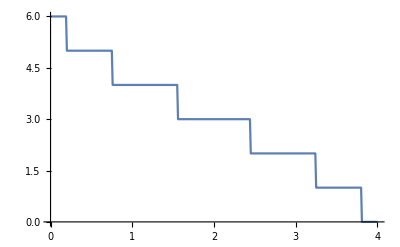

```mathematica
pris8=ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,6]]},{ω,Range[0,4,0.01]}]]
```

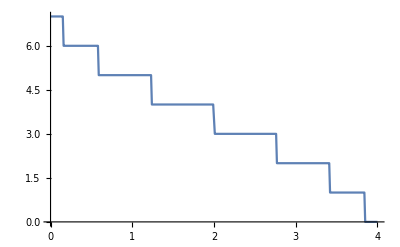

```mathematica
pris7=ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,7]]},{ω,Range[0,4,0.01]}]]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.33333×10^7+0. ⅈ,0.-0.000111111 ⅈ,-3.33333×10^7+0. ⅈ,0.+0.0000888889 ⅈ,3.33333×10^7+0. ⅈ},{0.-0.000111111 ⅈ,0.333333+0. ⅈ,0.-0.0000222222 ⅈ,0.333333+0. ⅈ,0.+0.0000888889 ⅈ},{-3.33333×10^7+0. ⅈ,0.-0.0000222222 ⅈ,3.33333×10^7+0. ⅈ,0.-0.0000222222 ⅈ,-3.33333×10^7+0. ⅈ},{0.+0.0000888889 ⅈ,0.333333+0. ⅈ,0.-0.0000222222 ⅈ,0.333333+0. ⅈ,0.-0.000111111 ⅈ},{3.33333×10^7+0. ⅈ,0.+0.0000888889 ⅈ,-3.33333×10^7+0. ⅈ,0.-0.000111111 ⅈ,3.33333×10^7+0. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.33333×10^6+0. ⅈ,0.-0.000380779 ⅈ,-8.33333×10^6+0. ⅈ,0.+0.000215302 ⅈ,8.33333×10^6+0. ⅈ},{0.-0.000377587 ⅈ,0.333333+0. ⅈ,0.-0.000155746 ⅈ,0.333333+0. ⅈ,0.+0.000222413 ⅈ},{-8.33333×10^6+0. ⅈ,0.-0.000152554 ⅈ,8.33333×10^6+0. ⅈ,0.-0.000148635 ⅈ,-8.33333×10^6+0. ⅈ},{0.+0.000222413 ⅈ,0.333333+0. ⅈ,0.-0.000155746 ⅈ,0.333333+0. ⅈ,0.-0.000377587 ⅈ},{8.33333×10^6+0. ⅈ,0.+0.000219221 ⅈ,-8.33333×10^6+0. ⅈ,0.-0.000384698 ⅈ,8.33333×10^6+0. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.76191×10^6+0. ⅈ,0.-0.000646988 ⅈ,-4.76191×10^6+0. ⅈ,0.+0.000356064 ⅈ,4.76191×10^6+0. ⅈ},{0.-0.000644265 ⅈ,0.333333+0. ⅈ,0.-0.000289068 ⅈ,0.333333+0. ⅈ,0.+0.000355735 ⅈ},{-4.76191×10^6+0. ⅈ,0.-0.000286345 ⅈ,4.76191×10^6+0. ⅈ,0.-0.000289397 ⅈ,-4.76191×10^6+0. ⅈ},{0.+0.000355735 ⅈ,0.333333+0. ⅈ,0.-0.000289068 ⅈ,0.333333+0. ⅈ,0.-0.000644265 ⅈ},{4.76191×10^6+0. ⅈ,0.+0.000353012 ⅈ,-4.76191×10^6+0. ⅈ,0.-0.000643936 ⅈ,4.76191×10^6+0. ⅈ}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

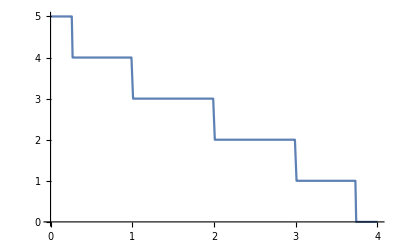

```mathematica
pris5=ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,5]]},{ω,Range[0,4,0.01]}]]
```

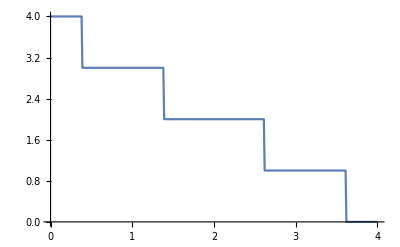

```mathematica
pris4=ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,4]]},{ω,Range[0,4,0.01]}]]
```

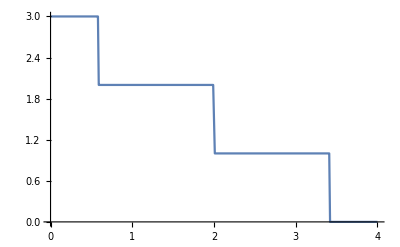

```mathematica
pris4=ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,3]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Do[Export["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/lead/sr"<>ToString[ω]<>".dat",SR[ω,0.0001,1,0,20]],{ω,Range[0,4,0.01]}]
```

```mathematica
Sr=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/lead/sr"<>ToString[ω]<>".dat"]],{ω,Range[0,4,0.01]}]
```

{1}
 |  |  |  |

```mathematica
Sr[[1]]
```

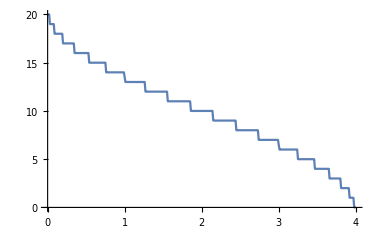

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,20]]},{ω,Range[0,4,0.01]}]]
```

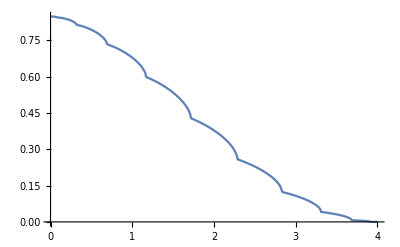

```mathematica
ListLinePlot[Table[{ω,-Im[SL[ω,0.0001,1,0,10][[1,1]]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Clear[imp,imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp,list,b,surface]
```

```mathematica
μ1=RandomInteger[{1,10}]; μ2=RandomInteger[{1,10}];μ3=RandomInteger[{1,10}]; μ4=RandomInteger[{1,10}];μ5=RandomInteger[{1,10}]; μ6=RandomInteger[{1,10}]; μ7=RandomInteger[{1,10}];μ8=RandomInteger[{1,10}];μ9=RandomInteger[{1,10}]; μ10=RandomInteger[{1,10}]; μ11=RandomInteger[{1,10}];μ12=RandomInteger[{1,10}];μ13=RandomInteger[{1,10}];μ14=RandomInteger[{1,10}]
```

3

```mathematica
surface[ω_,δ_,t_,ϵ_,m_,ϵ1_]:=surface[ω,δ,t,ϵ,m,ϵ1]=Module[{Tin=T[1,m],J=SL[ω,δ,t,ϵ,m](*,μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}],μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}],μ14=RandomInteger[{1,m}]*)},
imp1:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*δ-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*δ-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*δ-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*δ-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*δ-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*δ-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*δ-0]]];
list={{imp,imp,imp,imp1,imp3,imp5,imp14,imp,imp,imp,imp2,imp,imp5,imp,imp4,imp,imp12,imp1,imp,imp,imp8,imp,imp,imp8,imp3,imp,imp,imp,imp,imp,imp4,imp,imp11,imp3,imp,imp,imp,imp,imp,imp13,imp7,imp,imp4,imp7,imp9,imp,imp2,imp14,imp5,imp,imp,imp,imp,imp13,imp6,imp,imp,imp10,imp11,imp,imp12,imp,imp,imp14,imp,imp,imp,imp11,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp13,imp9,imp10,imp2,imp10,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp9}};
b= 
Table[Module[{(*J=SL[ω,δ,t,ϵ,m]*)},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,n}];
 J=J],{n,100}];
b]
```

```mathematica
Timing[surface[-0.5,0.0001,1,0,10,0]]
```

{0.000032,{1}}
 |  |  |  |

```mathematica
Timing[s[-0.5]]
```

{0.000042,{1}}
 |  |  |  |

```mathematica
s[ω_]:=s[ω]=Table[surface[ω,δ,1,0,10,0,n],{n,100}]
```

```mathematica
il[ω_,δ_,t_,ϵ_,m_,ϵ1_,n_]:= Inverse[IdentityMatrix[m]-surface[ω,δ,t,ϵ,m,ϵ1][[100]].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].surface[ω,δ,t,ϵ,m,ϵ1][[100]]
```

```mathematica
Timing[il[.11,0.0001,1,0,10,0,100]]
```

{0.244872,{{0.0422384-0.604665 ⅈ,-0.0810914+0.0119064 ⅈ,0.113288-0.116121 ⅈ,-0.136378-0.0398428 ⅈ,0.148354+0.014468 ⅈ,-0.148366-0.0747759 ⅈ,0.136321+0.0586233 ⅈ,-0.113266-0.0697298 ⅈ,0.0810169+0.0455073 ⅈ,-0.0422212-0.0280837 ⅈ},{-0.0810914+0.0119064 ⅈ,0.155526-0.720786 ⅈ,-0.217469-0.0279365 ⅈ,0.261642-0.101653 ⅈ,-0.284744-0.114619 ⅈ,0.284675+0.0730913 ⅈ,-0.261632-0.144506 ⅈ,0.217338+0.104131 ⅈ,-0.155487-0.0978135 ⅈ,0.0810169+0.0455073 ⅈ},{0.113288-0.116121 ⅈ,-0.217469-0.0279365 ⅈ,0.303881-0.706318 ⅈ,-0.365835-0.102712 ⅈ,0.397963-0.0430298 ⅈ,-0.398009-0.184349 ⅈ,0.365692+0.118599 ⅈ,-0.303853-0.172589 ⅈ,0.217338+0.104131 ⅈ,-0.113266-0.0697298 ⅈ},{-0.136378-0.0398428 ⅈ,0.261642-0.101653 ⅈ,-0.365835-0.102712 ⅈ,0.440201-0.647695 ⅈ,-0.479101-0.172442 ⅈ,0.47898+0.00247752 ⅈ,-0.440231-0.212432 ⅈ,0.365692+0.118599 ⅈ,-0.261632-0.144506 ⅈ,0.136321+0.0586233 ⅈ},{0.148354+0.014468 ⅈ,-0.284744-0.114619 ⅈ,0.397963-0.0430298 ⅈ,-0.479101-0.172442 ⅈ,0.521218-0.602187 ⅈ,-0.521322-0.200526 ⅈ,0.47898+0.00247752 ⅈ,-0.398009-0.184349 ⅈ,0.284675+0.0730913 ⅈ,-0.148366-0.0747759 ⅈ},{-0.148366-0.0747759 ⅈ,0.284675+0.0730913 ⅈ,-0.398009-0.184349 ⅈ,0.47898+0.00247752 ⅈ,-0.521322-0.200526 ⅈ,0.521218-0.602187 ⅈ,-0.479101-0.172442 ⅈ,0.397963-0.0430298 ⅈ,-0.284744-0.114619 ⅈ,0.148354+0.014468 ⅈ},{0.136321+0.0586233 ⅈ,-0.261632-0.144506 ⅈ,0.365692+0.118599 ⅈ,-0.440231-0.212432 ⅈ,0.47898+0.00247752 ⅈ,-0.479101-0.172442 ⅈ,0.440201-0.647695 ⅈ,-0.365835-0.102712 ⅈ,0.261642-0.101653 ⅈ,-0.136378-0.0398428 ⅈ},{-0.113266-0.0697298 ⅈ,0.217338+0.104131 ⅈ,-0.303853-0.172589 ⅈ,0.365692+0.118599 ⅈ,-0.398009-0.184349 ⅈ,0.397963-0.0430298 ⅈ,-0.365835-0.102712 ⅈ,0.303881-0.706318 ⅈ,-0.217469-0.0279365 ⅈ,0.113288-0.116121 ⅈ},{0.0810169+0.0455073 ⅈ,-0.155487-0.0978135 ⅈ,0.217338+0.104131 ⅈ,-0.261632-0.144506 ⅈ,0.284675+0.0730913 ⅈ,-0.284744-0.114619 ⅈ,0.261642-0.101653 ⅈ,-0.217469-0.0279365 ⅈ,0.155526-0.720786 ⅈ,-0.0810914+0.0119064 ⅈ},{-0.0422212-0.0280837 ⅈ,0.0810169+0.0455073 ⅈ,-0.113266-0.0697298 ⅈ,0.136321+0.0586233 ⅈ,-0.148366-0.0747759 ⅈ,0.148354+0.014468 ⅈ,-0.136378-0.0398428 ⅈ,0.113288-0.116121 ⅈ,-0.0810914+0.0119064 ⅈ,0.0422384-0.604665 ⅈ}}}

```mathematica
gnonlocalik[ω_,δ_,t_,ϵ_,m_,ϵ1_,k_,i_]:=Module[{Tin=T[t,m]},gik=Module[{J=surface[ω,δ,t,ϵ,m,ϵ1][[k+1]].T[t,m].surface[ω,δ,t,ϵ,m,ϵ1][[k]]},Do[J=surface[ω,δ,t,ϵ,m,ϵ1][[l]].T[t,m].J,{l,k+2,i}];J=J];il[ω,δ,t,ϵ,m,ϵ1,i].T[t,m].gik]
```

```mathematica
Timing[gnonlocalik[0,0.0001,1,0,10,0.0,1,100]]
```

{0.181724,{{0.+0.0129019 ⅈ,0.000172306+0. ⅈ,0.+0.0412236 ⅈ,0.000364472+0. ⅈ,0.+0.0794421 ⅈ,0.000618544+0. ⅈ,0.+0.148866 ⅈ,0.00108833+0. ⅈ,0.+0.411648 ⅈ,-0.496802+0. ⅈ},{0.000172306+0. ⅈ,0.+0.0541255 ⅈ,0.000536778+0. ⅈ,0.+0.120666 ⅈ,0.000983016+0. ⅈ,0.+0.228308 ⅈ,0.00170687+0. ⅈ,0.+0.560514 ⅈ,-0.495714+0. ⅈ,0.+0.411648 ⅈ},{0.+0.0412236 ⅈ,0.000536778+0. ⅈ,0.+0.133568 ⅈ,0.00115532+0. ⅈ,0.+0.269531 ⅈ,0.00207135+0. ⅈ,0.+0.639956 ⅈ,-0.495095+0. ⅈ,0.+0.560514 ⅈ,0.00108833+0. ⅈ},{0.000364472+0. ⅈ,0.+0.120666 ⅈ,0.00115532+0. ⅈ,0.+0.282433 ⅈ,0.00224365+0. ⅈ,0.+0.68118 ⅈ,-0.494731+0. ⅈ,0.+0.639956 ⅈ,0.00170687+0. ⅈ,0.+0.148866 ⅈ},{0.+0.0794421 ⅈ,0.000983016+0. ⅈ,0.+0.269531 ⅈ,0.00224365+0. ⅈ,0.+0.694082 ⅈ,-0.494559+0. ⅈ,0.+0.68118 ⅈ,0.00207135+0. ⅈ,0.+0.228308 ⅈ,0.000618544+0. ⅈ},{0.000618544+0. ⅈ,0.+0.228308 ⅈ,0.00207135+0. ⅈ,0.+0.68118 ⅈ,-0.494559+0. ⅈ,0.+0.694082 ⅈ,0.00224365+0. ⅈ,0.+0.269531 ⅈ,0.000983016+0. ⅈ,0.+0.0794421 ⅈ},{0.+0.148866 ⅈ,0.00170687+0. ⅈ,0.+0.639956 ⅈ,-0.494731+0. ⅈ,0.+0.68118 ⅈ,0.00224365+0. ⅈ,0.+0.282433 ⅈ,0.00115532+0. ⅈ,0.+0.120666 ⅈ,0.000364472+0. ⅈ},{0.00108833+0. ⅈ,0.+0.560514 ⅈ,-0.495095+0. ⅈ,0.+0.639956 ⅈ,0.00207135+0. ⅈ,0.+0.269531 ⅈ,0.00115532+0. ⅈ,0.+0.133568 ⅈ,0.000536778+0. ⅈ,0.+0.0412236 ⅈ},{0.+0.411648 ⅈ,-0.495714+0. ⅈ,0.+0.560514 ⅈ,0.00170687+0. ⅈ,0.+0.228308 ⅈ,0.000983016+0. ⅈ,0.+0.120666 ⅈ,0.000536778+0. ⅈ,0.+0.0541255 ⅈ,0.000172306+0. ⅈ},{-0.496802+0. ⅈ,0.+0.411648 ⅈ,0.00108833+0. ⅈ,0.+0.148866 ⅈ,0.000618544+0. ⅈ,0.+0.0794421 ⅈ,0.000364472+0. ⅈ,0.+0.0412236 ⅈ,0.000172306+0. ⅈ,0.+0.0129019 ⅈ}}}

```mathematica
Ε[ω_]:=Ε[ω]= T[1,10].SL[ω,0.0001,1,0,10].T[1,10]
```

```mathematica
Γ[ω_]:= ⅈ(Ε[ω]-ConjugateTranspose[Ε[ω]])
```

```mathematica
TRA[ω_,ϵ1_]:=Abs[Tr[Γ[ω].gnonlocalik[ω,0.0001,1,0,10,ϵ1,1,50].Γ[ω].ConjugateTranspose[gnonlocalik[ω,0.0001,1,0,10,ϵ1,1,50]]]]
```

```mathematica
Timing[TRA[0,0]]
```

{0.394321,9.91043}

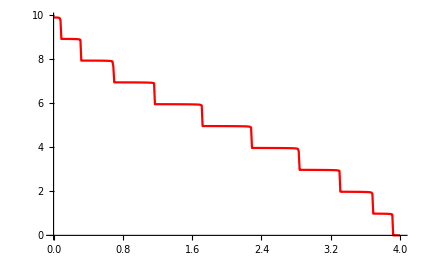

```mathematica
ListLinePlot[Table[{ω,TRA[ω,0]},{ω,Range[0,4,0.01]}],PlotStyle->Red]
```

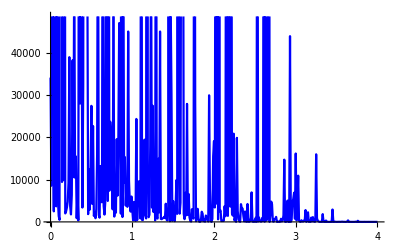

```mathematica
ListLinePlot[Table[{ω,TRA2[ω,0.3]},{ω,Range[0,4,0.01]}],PlotStyle->Blue]
```

```mathematica
Show[%276,%279]
```

```mathematica
TRA2[1,0.3]
```

2858.9

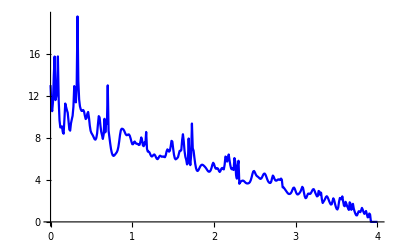

```mathematica
ListLinePlot[Table[{ω,TRA[ω,0.3]},{ω,Range[0,4,0.01]}],PlotStyle->Blue]
```

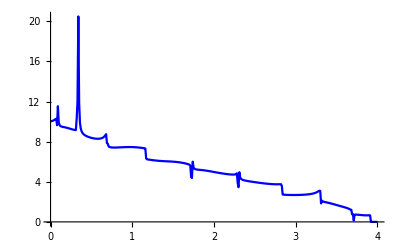

```mathematica
ListLinePlot[Table[{ω,TRA[ω,0.5]},{ω,Range[0,4,0.01]}],PlotStyle->Blue]
```

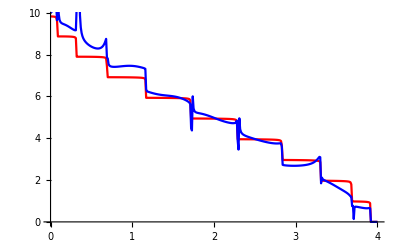

```mathematica
Show[%157,%163]
```

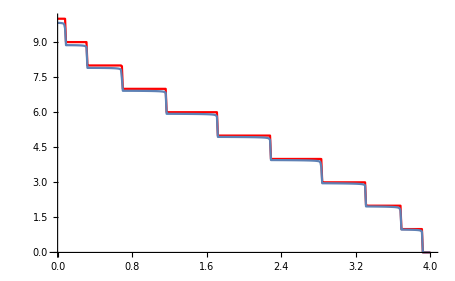

```mathematica
Show[ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,10]]},{ω,Range[0,4,0.01]}],PlotStyle->Red],%90]
```

```mathematica
greenfunctions[ω_,δ_,t_,ϵ_,m_,ϵ1_,START_,STOP_]:=Module[{Tin=T[1,m],J=SL[ω,δ,t,ϵ,m],b,il,gnk(*,μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}],μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}],μ14=RandomInteger[{1,m}]*)},
imp1:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*δ-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*δ-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*δ-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*δ-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*δ-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*δ-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*δ-0]]];
list={{imp,imp,imp,imp1,imp3,imp5,imp14,imp,imp,imp,imp2,imp,imp5,imp,imp4,imp,imp12,imp1,imp,imp,imp8,imp,imp,imp8,imp3,imp,imp,imp,imp,imp,imp4,imp,imp11,imp3,imp,imp,imp,imp,imp,imp13,imp7,imp,imp4,imp7,imp9,imp,imp2,imp14,imp5,imp,imp,imp,imp,imp13,imp6,imp,imp,imp10,imp11,imp,imp12,imp,imp,imp14,imp,imp,imp,imp11,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp13,imp9,imp10,imp2,imp10,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp,imp}};
b[n_]:=
Module[{(*J=SL[ω,δ,t,ϵ,m]*)},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,n}];
 J=J];
ξ=With[{},Table[b[n],{n,STOP+1}]];
ir:=Inverse[IdentityMatrix[10]-J.T[1,10].ξ[[101]].T[1,10]].J;
gnk[κ_,ι_,Τ_,Μ_]:=Module[{},
gik=Module[{φ=ξ[[κ]].T[1,10].ξ[[κ+1]]},Do[φ=φ.T[1,10].ξ[[l]],{l,κ+2,ι}];
φ=φ];
gik];
gnk[START,STOP,t,m]]
```

```mathematica
greenfunctions[0,0.0001,1,0,10,0,1,100]
```

{{0.000131234+0. ⅈ,0.+0.00251768 ⅈ,0.000418886+0. ⅈ,0.+0.00737844 ⅈ,0.000805518+0. ⅈ,0.+0.0238256 ⅈ,0.00150423+0. ⅈ,0.+0.169532 ⅈ,-0.495863+0. ⅈ,0.-0.843914 ⅈ},{0.+0.00251768 ⅈ,0.00055012+0. ⅈ,0.+0.00989612 ⅈ,0.0012244+0. ⅈ,0.+0.0312041 ⅈ,0.00230975+0. ⅈ,0.+0.193358 ⅈ,-0.494359+0. ⅈ,0.-0.674382 ⅈ,-0.495863+0. ⅈ},{0.000418886+0. ⅈ,0.+0.00989612 ⅈ,0.00135564+0. ⅈ,0.+0.0337218 ⅈ,0.00272863+0. ⅈ,0.+0.200736 ⅈ,-0.493554+0. ⅈ,0.-0.650557 ⅈ,-0.494359+0. ⅈ,0.+0.169532 ⅈ},{0.+0.00737844 ⅈ,0.0012244+0. ⅈ,0.+0.0337218 ⅈ,0.00285987+0. ⅈ,0.+0.203254 ⅈ,-0.493135+0. ⅈ,0.-0.643178 ⅈ,-0.493554+0. ⅈ,0.+0.193358 ⅈ,0.00150423+0. ⅈ},{0.000805518+0. ⅈ,0.+0.0312041 ⅈ,0.00272863+0. ⅈ,0.+0.203254 ⅈ,-0.493004+0. ⅈ,0.-0.640661 ⅈ,-0.493135+0. ⅈ,0.+0.200736 ⅈ,0.00230975+0. ⅈ,0.+0.0238256 ⅈ},{0.+0.0238256 ⅈ,0.00230975+0. ⅈ,0.+0.200736 ⅈ,-0.493135+0. ⅈ,0.-0.640661 ⅈ,-0.493004+0. ⅈ,0.+0.203254 ⅈ,0.00272863+0. ⅈ,0.+0.0312041 ⅈ,0.000805518+0. ⅈ},{0.00150423+0. ⅈ,0.+0.193358 ⅈ,-0.493554+0. ⅈ,0.-0.643178 ⅈ,-0.493135+0. ⅈ,0.+0.203254 ⅈ,0.00285987+0. ⅈ,0.+0.0337218 ⅈ,0.0012244+0. ⅈ,0.+0.00737844 ⅈ},{0.+0.169532 ⅈ,-0.494359+0. ⅈ,0.-0.650557 ⅈ,-0.493554+0. ⅈ,0.+0.200736 ⅈ,0.00272863+0. ⅈ,0.+0.0337218 ⅈ,0.00135564+0. ⅈ,0.+0.00989612 ⅈ,0.000418886+0. ⅈ},{-0.495863+0. ⅈ,0.-0.674382 ⅈ,-0.494359+0. ⅈ,0.+0.193358 ⅈ,0.00230975+0. ⅈ,0.+0.0312041 ⅈ,0.0012244+0. ⅈ,0.+0.00989612 ⅈ,0.00055012+0. ⅈ,0.+0.00251768 ⅈ},{0.-0.843914 ⅈ,-0.495863+0. ⅈ,0.+0.169532 ⅈ,0.00150423+0. ⅈ,0.+0.0238256 ⅈ,0.000805518+0. ⅈ,0.+0.00737844 ⅈ,0.000418886+0. ⅈ,0.+0.00251768 ⅈ,0.000131234+0. ⅈ}}

```mathematica
gik111[κ_,ι_]:=Module[{φ=b1[κ].V.b1[κ+1]},Do[φ=φ.V.b1[l],{l,κ+2,ι}];
φ=φ]
```

```mathematica
gik111[1,100]
```

b1[1].V.b1[2].V.b1[3].V.b1[4].V.b1[5].V.b1[6].V.b1[7].V.b1[8].V.b1[9].V.b1[10].V.b1[11].V.b1[12].V.b1[13].V.b1[14].V.b1[15].V.b1[16].V.b1[17].V.b1[18].V.b1[19].V.b1[20].V.b1[21].V.b1[22].V.b1[23].V.b1[24].V.b1[25].V.b1[26].V.b1[27].V.b1[28].V.b1[29].V.b1[30].V.b1[31].V.b1[32].V.b1[33].V.b1[34].V.b1[35].V.b1[36].V.b1[37].V.b1[38].V.b1[39].V.b1[40].V.b1[41].V.b1[42].V.b1[43].V.b1[44].V.b1[45].V.b1[46].V.b1[47].V.b1[48].V.b1[49].V.b1[50].V.b1[51].V.b1[52].V.b1[53].V.b1[54].V.b1[55].V.b1[56].V.b1[57].V.b1[58].V.b1[59].V.b1[60].V.b1[61].V.b1[62].V.b1[63].V.b1[64].V.b1[65].V.b1[66].V.b1[67].V.b1[68].V.b1[69].V.b1[70].V.b1[71].V.b1[72].V.b1[73].V.b1[74].V.b1[75].V.b1[76].V.b1[77].V.b1[78].V.b1[79].V.b1[80].V.b1[81].V.b1[82].V.b1[83].V.b1[84].V.b1[85].V.b1[86].V.b1[87].V.b1[88].V.b1[89].V.b1[90].V.b1[91].V.b1[92].V.b1[93].V.b1[94].V.b1[95].V.b1[96].V.b1[97].V.b1[98].V.b1[99].V.b1[100]

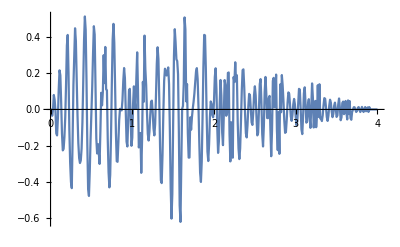

```mathematica
ListLinePlot[Table[{ω,-Im[greenfunctions[ω,0.0001,1,0,10,0,1,100][[1,1]]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
TRA2[ω_,ϵ1_]:=Abs[Tr[Γ[ω].greenfunctions[ω,0.0001,1,0,10,ϵ1,1,100].Γ[ω].ConjugateTranspose[greenfunctions[ω,0.0001,1,0,10,ϵ1,1,100]]]]
```

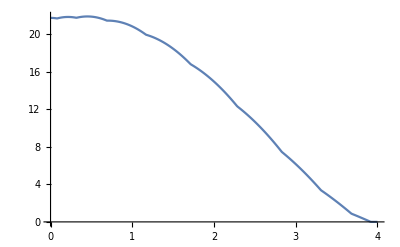

```mathematica
ListLinePlot[Table[{ω,TRA2[ω,0]},{ω,Range[0,4,0.01]}]]
```

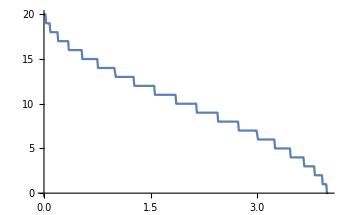

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0,20]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
LEFT[1.6,0.0001,1,0,20]
```

{{0.483268-0.487021 ⅈ,-0.109865-0.395884 ⅈ,-0.216368+0.000104526 ⅈ,0.0025665+0.124646 ⅈ,0.0728843-0.0143304 ⅈ,-0.0208033-0.0568908 ⅈ,-0.0338025+0.0255238 ⅈ,0.0227662+0.0297846 ⅈ,0.0142494-0.0274045 ⅈ,-0.0196025-0.0134178 ⅈ,-0.00317989+0.025796 ⅈ,0.0145215+0.00224635 ⅈ,-0.00274882-0.0222819 ⅈ,-0.00905197+0.00570799 ⅈ,0.00507448+0.0175832 ⅈ,0.00416245-0.0112749 ⅈ,-0.00481226-0.0121144 ⅈ,-0.000529404+0.0148401 ⅈ,0.00283621+0.00617119 ⅈ,-0.00139983-0.0165858 ⅈ},{-0.109865-0.395884 ⅈ,0.266901-0.486916 ⅈ,-0.107298-0.271239 ⅈ,-0.143483-0.0142259 ⅈ,-0.0182368+0.0677547 ⅈ,0.0390818+0.0111934 ⅈ,0.00196293-0.0271062 ⅈ,-0.0195531-0.00188066 ⅈ,0.00316367+0.0163668 ⅈ,0.0110695-0.00160844 ⅈ,-0.00508103-0.0111714 ⅈ,-0.00592871+0.0035141 ⅈ,0.00546951+0.00795434 ⅈ,0.00232566-0.00469874 ⅈ,-0.00488951-0.00556693 ⅈ,0.00026222+0.00546882 ⅈ,0.00363305+0.00356519 ⅈ,-0.00197605-0.00594318 ⅈ,-0.00192923-0.00174572 ⅈ,0.00283621+0.00617119 ⅈ},{-0.216368+0.000104526 ⅈ,-0.107298-0.271239 ⅈ,0.339785-0.501246 ⅈ,-0.128101-0.32813 ⅈ,-0.177286+0.0112979 ⅈ,0.00452942+0.0975393 ⅈ,0.0533312-0.0162111 ⅈ,-0.0176396-0.040524 ⅈ,-0.022733+0.0239154 ⅈ,0.0176851+0.0186132 ⅈ,0.00832069-0.0238904 ⅈ,-0.014133-0.00546346 ⅈ,-0.000854227+0.0210973 ⅈ,0.00963196-0.00332058 ⅈ,-0.0024866-0.0168131 ⅈ,-0.00541892+0.00927318 ⅈ,0.00309843+0.01164 ⅈ,0.00223322-0.0130206 ⅈ,-0.00197605-0.00594318 ⅈ,-0.000529404+0.0148401 ⅈ},{0.0025665+0.124646 ⅈ,-0.143483-0.0142259 ⅈ,-0.128101-0.32813 ⅈ,0.305982-0.475723 ⅈ,-0.105335-0.298345 ⅈ,-0.163036-0.0161065 ⅈ,-0.0150731+0.0841215 ⅈ,0.0501513+0.00958496 ⅈ,-0.0031181-0.0382777 ⅈ,-0.0254818+0.00163344 ⅈ,0.00863318+0.0243211 ⅈ,0.0133952-0.00630718 ⅈ,-0.00997055-0.0167384 ⅈ,-0.00566649+0.00898292 ⅈ,0.00910256+0.0115195 ⅈ,0.000349615-0.0106419 ⅈ,-0.00681875-0.00731265 ⅈ,0.00309843+0.01164 ⅈ,0.00363305+0.00356519 ⅈ,-0.00481226-0.0121144 ⅈ},{0.0728843-0.0143304 ⅈ,-0.0182368+0.0677547 ⅈ,-0.177286+0.0112979 ⅈ,-0.105335-0.298345 ⅈ,0.320232-0.503127 ⅈ,-0.124938-0.311763 ⅈ,-0.166216+0.00968949 ⅈ,-0.000551608+0.0863679 ⅈ,0.0474024-0.012697 ⅈ,-0.0121701-0.0325697 ⅈ,-0.0204074+0.0192166 ⅈ,0.0127956+0.0130462 ⅈ,0.0085829-0.0184216 ⅈ,-0.0104999-0.00189826 ⅈ,-0.00283028+0.0151541 ⅈ,0.00770273-0.0050663 ⅈ,0.000349615-0.0106419 ⅈ,-0.00541892+0.00927318 ⅈ,0.00026222+0.00546882 ⅈ,0.00416245-0.0112749 ⅈ},{-0.0208033-0.0568908 ⅈ,0.0390818+0.0111934 ⅈ,0.00452942+0.0975393 ⅈ,-0.163036-0.0161065 ⅈ,-0.124938-0.311763 ⅈ,0.317052-0.477331 ⅈ,-0.110416-0.309517 ⅈ,-0.168965-0.0125924 ⅈ,-0.00960357+0.0920758 ⅈ,0.0524769+0.00488622 ⅈ,-0.00800762-0.0438446 ⅈ,-0.0252196+0.00710226 ⅈ,0.0122662+0.0278863 ⅈ,0.0114191-0.0122504 ⅈ,-0.0118998-0.0184841 ⅈ,-0.00283028+0.0151541 ⅈ,0.00910256+0.0115195 ⅈ,-0.0024866-0.0168131 ⅈ,-0.00488951-0.00556693 ⅈ,0.00507448+0.0175832 ⅈ},{-0.0338025+0.0255238 ⅈ,0.00196293-0.0271062 ⅈ,0.0533312-0.0162111 ⅈ,-0.0150731+0.0841215 ⅈ,-0.166216+0.00968949 ⅈ,-0.110416-0.309517 ⅈ,0.314303-0.499613 ⅈ,-0.119468-0.303809 ⅈ,-0.163891+0.00499075 ⅈ,-0.00544112+0.0808009 ⅈ,0.0476647-0.00722815 ⅈ,-0.00853702-0.0290045 ⅈ,-0.0223834+0.0132734 ⅈ,0.0108664+0.0113005 ⅈ,0.0114191-0.0122504 ⅈ,-0.0104999-0.00189826 ⅈ,-0.00566649+0.00898292 ⅈ,0.00963196-0.00332058 ⅈ,0.00232566-0.00469874 ⅈ,-0.00905197+0.00570799 ⅈ},{0.0227662+0.0297846 ⅈ,-0.0195531-0.00188066 ⅈ,-0.0176396-0.040524 ⅈ,0.0501513+0.00958496 ⅈ,-0.000551608+0.0863679 ⅈ,-0.168965-0.0125924 ⅈ,-0.119468-0.303809 ⅈ,0.319378-0.48203 ⅈ,-0.115306-0.315083 ⅈ,-0.168703-0.00712362 ⅈ,-0.00597053+0.095641 ⅈ,0.0505009-0.00105696 ⅈ,-0.00993685-0.0455903 ⅈ,-0.0223834+0.0132734 ⅈ,0.0122662+0.0278863 ⅈ,0.0085829-0.0184216 ⅈ,-0.00997055-0.0167384 ⅈ,-0.000854227+0.0210973 ⅈ,0.00546951+0.00795434 ⅈ,-0.00274882-0.0222819 ⅈ},{0.0142494-0.0274045 ⅈ,0.00316367+0.0163668 ⅈ,-0.022733+0.0239154 ⅈ,-0.0031181-0.0382777 ⅈ,0.0474024-0.012697 ⅈ,-0.00960357+0.0920758 ⅈ,-0.163891+0.00499075 ⅈ,-0.115306-0.315083 ⅈ,0.314565-0.494144 ⅈ,-0.115835-0.300243 ⅈ,-0.165867-0.000952434 ⅈ,-0.00737036+0.0790552 ⅈ,0.0505009-0.00105696 ⅈ,-0.00853702-0.0290045 ⅈ,-0.0252196+0.00710226 ⅈ,0.0127956+0.0130462 ⅈ,0.0133952-0.00630718 ⅈ,-0.014133-0.00546346 ⅈ,-0.00592871+0.0035141 ⅈ,0.0145215+0.00224635 ⅈ},{-0.0196025-0.0134178 ⅈ,0.0110695-0.00160844 ⅈ,0.0176851+0.0186132 ⅈ,-0.0254818+0.00163344 ⅈ,-0.0121701-0.0325697 ⅈ,0.0524769+0.00488622 ⅈ,-0.00544112+0.0808009 ⅈ,-0.168703-0.00712362 ⅈ,-0.115835-0.300243 ⅈ,0.317402-0.487973 ⅈ,-0.117235-0.316829 ⅈ,-0.165867-0.000952434 ⅈ,-0.00597053+0.095641 ⅈ,0.0476647-0.00722815 ⅈ,-0.00800762-0.0438446 ⅈ,-0.0204074+0.0192166 ⅈ,0.00863318+0.0243211 ⅈ,0.00832069-0.0238904 ⅈ,-0.00508103-0.0111714 ⅈ,-0.00317989+0.025796 ⅈ},{-0.00317989+0.025796 ⅈ,-0.00508103-0.0111714 ⅈ,0.00832069-0.0238904 ⅈ,0.00863318+0.0243211 ⅈ,-0.0204074+0.0192166 ⅈ,-0.00800762-0.0438446 ⅈ,0.0476647-0.00722815 ⅈ,-0.00597053+0.095641 ⅈ,-0.165867-0.000952434 ⅈ,-0.117235-0.316829 ⅈ,0.317402-0.487973 ⅈ,-0.115835-0.300243 ⅈ,-0.168703-0.00712362 ⅈ,-0.00544112+0.0808009 ⅈ,0.0524769+0.00488622 ⅈ,-0.0121701-0.0325697 ⅈ,-0.0254818+0.00163344 ⅈ,0.0176851+0.0186132 ⅈ,0.0110695-0.00160844 ⅈ,-0.0196025-0.0134178 ⅈ},{0.0145215+0.00224635 ⅈ,-0.00592871+0.0035141 ⅈ,-0.014133-0.00546346 ⅈ,0.0133952-0.00630718 ⅈ,0.0127956+0.0130462 ⅈ,-0.0252196+0.00710226 ⅈ,-0.00853702-0.0290045 ⅈ,0.0505009-0.00105696 ⅈ,-0.00737036+0.0790552 ⅈ,-0.165867-0.000952434 ⅈ,-0.115835-0.300243 ⅈ,0.314565-0.494144 ⅈ,-0.115306-0.315083 ⅈ,-0.163891+0.00499075 ⅈ,-0.00960357+0.0920758 ⅈ,0.0474024-0.012697 ⅈ,-0.0031181-0.0382777 ⅈ,-0.022733+0.0239154 ⅈ,0.00316367+0.0163668 ⅈ,0.0142494-0.0274045 ⅈ},{-0.00274882-0.0222819 ⅈ,0.00546951+0.00795434 ⅈ,-0.000854227+0.0210973 ⅈ,-0.00997055-0.0167384 ⅈ,0.0085829-0.0184216 ⅈ,0.0122662+0.0278863 ⅈ,-0.0223834+0.0132734 ⅈ,-0.00993685-0.0455903 ⅈ,0.0505009-0.00105696 ⅈ,-0.00597053+0.095641 ⅈ,-0.168703-0.00712362 ⅈ,-0.115306-0.315083 ⅈ,0.319378-0.48203 ⅈ,-0.119468-0.303809 ⅈ,-0.168965-0.0125924 ⅈ,-0.000551608+0.0863679 ⅈ,0.0501513+0.00958496 ⅈ,-0.0176396-0.040524 ⅈ,-0.0195531-0.00188066 ⅈ,0.0227662+0.0297846 ⅈ},{-0.00905197+0.00570799 ⅈ,0.00232566-0.00469874 ⅈ,0.00963196-0.00332058 ⅈ,-0.00566649+0.00898292 ⅈ,-0.0104999-0.00189826 ⅈ,0.0114191-0.0122504 ⅈ,0.0108664+0.0113005 ⅈ,-0.0223834+0.0132734 ⅈ,-0.00853702-0.0290045 ⅈ,0.0476647-0.00722815 ⅈ,-0.00544112+0.0808009 ⅈ,-0.163891+0.00499075 ⅈ,-0.119468-0.303809 ⅈ,0.314303-0.499613 ⅈ,-0.110416-0.309517 ⅈ,-0.166216+0.00968949 ⅈ,-0.0150731+0.0841215 ⅈ,0.0533312-0.0162111 ⅈ,0.00196293-0.0271062 ⅈ,-0.0338025+0.0255238 ⅈ},{0.00507448+0.0175832 ⅈ,-0.00488951-0.00556693 ⅈ,-0.0024866-0.0168131 ⅈ,0.00910256+0.0115195 ⅈ,-0.00283028+0.0151541 ⅈ,-0.0118998-0.0184841 ⅈ,0.0114191-0.0122504 ⅈ,0.0122662+0.0278863 ⅈ,-0.0252196+0.00710226 ⅈ,-0.00800762-0.0438446 ⅈ,0.0524769+0.00488622 ⅈ,-0.00960357+0.0920758 ⅈ,-0.168965-0.0125924 ⅈ,-0.110416-0.309517 ⅈ,0.317052-0.477331 ⅈ,-0.124938-0.311763 ⅈ,-0.163036-0.0161065 ⅈ,0.00452942+0.0975393 ⅈ,0.0390818+0.0111934 ⅈ,-0.0208033-0.0568908 ⅈ},{0.00416245-0.0112749 ⅈ,0.00026222+0.00546882 ⅈ,-0.00541892+0.00927318 ⅈ,0.000349615-0.0106419 ⅈ,0.00770273-0.0050663 ⅈ,-0.00283028+0.0151541 ⅈ,-0.0104999-0.00189826 ⅈ,0.0085829-0.0184216 ⅈ,0.0127956+0.0130462 ⅈ,-0.0204074+0.0192166 ⅈ,-0.0121701-0.0325697 ⅈ,0.0474024-0.012697 ⅈ,-0.000551608+0.0863679 ⅈ,-0.166216+0.00968949 ⅈ,-0.124938-0.311763 ⅈ,0.320232-0.503127 ⅈ,-0.105335-0.298345 ⅈ,-0.177286+0.0112979 ⅈ,-0.0182368+0.0677547 ⅈ,0.0728843-0.0143304 ⅈ},{-0.00481226-0.0121144 ⅈ,0.00363305+0.00356519 ⅈ,0.00309843+0.01164 ⅈ,-0.00681875-0.00731265 ⅈ,0.000349615-0.0106419 ⅈ,0.00910256+0.0115195 ⅈ,-0.00566649+0.00898292 ⅈ,-0.00997055-0.0167384 ⅈ,0.0133952-0.00630718 ⅈ,0.00863318+0.0243211 ⅈ,-0.0254818+0.00163344 ⅈ,-0.0031181-0.0382777 ⅈ,0.0501513+0.00958496 ⅈ,-0.0150731+0.0841215 ⅈ,-0.163036-0.0161065 ⅈ,-0.105335-0.298345 ⅈ,0.305982-0.475723 ⅈ,-0.128101-0.32813 ⅈ,-0.143483-0.0142259 ⅈ,0.0025665+0.124646 ⅈ},{-0.000529404+0.0148401 ⅈ,-0.00197605-0.00594318 ⅈ,0.00223322-0.0130206 ⅈ,0.00309843+0.01164 ⅈ,-0.00541892+0.00927318 ⅈ,-0.0024866-0.0168131 ⅈ,0.00963196-0.00332058 ⅈ,-0.000854227+0.0210973 ⅈ,-0.014133-0.00546346 ⅈ,0.00832069-0.0238904 ⅈ,0.0176851+0.0186132 ⅈ,-0.022733+0.0239154 ⅈ,-0.0176396-0.040524 ⅈ,0.0533312-0.0162111 ⅈ,0.00452942+0.0975393 ⅈ,-0.177286+0.0112979 ⅈ,-0.128101-0.32813 ⅈ,0.339785-0.501246 ⅈ,-0.107298-0.271239 ⅈ,-0.216368+0.000104526 ⅈ},{0.00283621+0.00617119 ⅈ,-0.00192923-0.00174572 ⅈ,-0.00197605-0.00594318 ⅈ,0.00363305+0.00356519 ⅈ,0.00026222+0.00546882 ⅈ,-0.00488951-0.00556693 ⅈ,0.00232566-0.00469874 ⅈ,0.00546951+0.00795434 ⅈ,-0.00592871+0.0035141 ⅈ,-0.00508103-0.0111714 ⅈ,0.0110695-0.00160844 ⅈ,0.00316367+0.0163668 ⅈ,-0.0195531-0.00188066 ⅈ,0.00196293-0.0271062 ⅈ,0.0390818+0.0111934 ⅈ,-0.0182368+0.0677547 ⅈ,-0.143483-0.0142259 ⅈ,-0.107298-0.271239 ⅈ,0.266901-0.486916 ⅈ,-0.109865-0.395884 ⅈ},{-0.00139983-0.0165858 ⅈ,0.00283621+0.00617119 ⅈ,-0.000529404+0.0148401 ⅈ,-0.00481226-0.0121144 ⅈ,0.00416245-0.0112749 ⅈ,0.00507448+0.0175832 ⅈ,-0.00905197+0.00570799 ⅈ,-0.00274882-0.0222819 ⅈ,0.0145215+0.00224635 ⅈ,-0.00317989+0.025796 ⅈ,-0.0196025-0.0134178 ⅈ,0.0142494-0.0274045 ⅈ,0.0227662+0.0297846 ⅈ,-0.0338025+0.0255238 ⅈ,-0.0208033-0.0568908 ⅈ,0.0728843-0.0143304 ⅈ,0.0025665+0.124646 ⅈ,-0.216368+0.000104526 ⅈ,-0.109865-0.395884 ⅈ,0.483268-0.487021 ⅈ}}

```mathematica
SL[1,0.0001,1,0,20]
```

{{0.382877-0.662623 ⅈ,-0.319165-0.3419 ⅈ,-0.168162+0.144309 ⅈ,0.0976838+0.0572382 ⅈ,-0.0149232-0.0709611 ⅈ,-0.0368604+0.0288084 ⅈ,0.0411655+0.021371 ⅈ,-0.012892-0.0361553 ⅈ,-0.0173503+0.014507 ⅈ,0.0262734+0.0153099 ⅈ,-0.0118928-0.0244316 ⅈ,-0.00967053+0.00838237 ⅈ,0.0196879+0.0133656 ⅈ,-0.0116494-0.0189072 ⅈ,-0.00541293+0.00478161 ⅈ,0.0161212+0.0128545 ⅈ,-0.0119284-0.0158668 ⅈ,-0.00246424+0.0021974 ⅈ,0.01399+0.013141 ⅈ,-0.0126796-0.0140993 ⅈ},{-0.319165-0.3419 ⅈ,0.214714-0.518314 ⅈ,-0.221481-0.284662 ⅈ,-0.183086+0.0733477 ⅈ,0.0608234+0.0860466 ⅈ,0.0262423-0.0495901 ⅈ,-0.0497524-0.0073469 ⅈ,0.0238152+0.035878 ⅈ,0.0133814-0.0208454 ⅈ,-0.0292431-0.00992463 ⅈ,0.0166029+0.0236922 ⅈ,0.00779509-0.0110661 ⅈ,-0.0213199-0.0105248 ⅈ,0.0142749+0.0181472 ⅈ,0.00447177-0.00605268 ⅈ,-0.0173413-0.0110852 ⅈ,0.0136569+0.0150519 ⅈ,0.00206162-0.00272576 ⅈ,-0.0151438-0.0119019 ⅈ,0.01399+0.013141 ⅈ},{-0.168162+0.144309 ⅈ,-0.221481-0.284662 ⅈ,0.199791-0.589275 ⅈ,-0.258342-0.255854 ⅈ,-0.14192+0.0947187 ⅈ,0.0479314+0.0498913 ⅈ,0.00889197-0.0350832 ⅈ,-0.023479+0.00796297 ⅈ,0.0119224+0.0114463 ⅈ,0.00371086-0.012463 ⅈ,-0.0095552+0.00344093 ⅈ,0.00495347+0.00478504 ⅈ,0.00238217-0.00628445 ⅈ,-0.00519876+0.00232969 ⅈ,0.00234656+0.00228037 ⅈ,0.00200753-0.00385528 ⅈ,-0.00335131+0.00205584 ⅈ,0.000977356+0.000952665 ⅈ,0.00206162-0.00272576 ⅈ,-0.00246424+0.0021974 ⅈ},{0.0976838+0.0572382 ⅈ,-0.183086+0.0733477 ⅈ,-0.258342-0.255854 ⅈ,0.240957-0.567904 ⅈ,-0.271234-0.292009 ⅈ,-0.15927+0.109226 ⅈ,0.0742048+0.0652012 ⅈ,-0.00300079-0.0595148 ⅈ,-0.0331496+0.0163453 ⅈ,0.0316103+0.0248119 ⅈ,-0.00793853-0.0313702 ⅈ,-0.0149681+0.00822253 ⅈ,0.0210746+0.0176396 ⅈ,-0.0095462-0.0221512 ⅈ,-0.007663+0.0045271 ⅈ,0.0163366+0.0154214 ⅈ,-0.010672-0.0179545 ⅈ,-0.00335131+0.00205584 ⅈ,0.0136569+0.0150519 ⅈ,-0.0119284-0.0158668 ⅈ},{-0.0149232-0.0709611 ⅈ,0.0608234+0.0860466 ⅈ,-0.14192+0.0947187 ⅈ,-0.271234-0.292009 ⅈ,0.223606-0.553397 ⅈ,-0.24496-0.276699 ⅈ,-0.171163+0.0847941 ⅈ,0.0645343+0.0735836 ⅈ,0.0166871-0.0461492 ⅈ,-0.0447989-0.00256186 ⅈ,0.0261974+0.0295935 ⅈ,0.00818263-0.0185157 ⅈ,-0.0268965-0.00764426 ⅈ,0.0186104+0.019837 ⅈ,0.00444379-0.00901022 ⅈ,-0.0203426-0.00957217 ⅈ,0.0163366+0.0154214 ⅈ,0.00200753-0.00385528 ⅈ,-0.0173413-0.0110852 ⅈ,0.0161212+0.0128545 ⅈ},{-0.0368604+0.0288084 ⅈ,0.0262423-0.0495901 ⅈ,0.0479314+0.0498913 ⅈ,-0.15927+0.109226 ⅈ,-0.24496-0.276699 ⅈ,0.211714-0.577829 ⅈ,-0.254631-0.268317 ⅈ,-0.151475+0.0981596 ⅈ,0.0528849+0.0546764 ⅈ,0.0112741-0.0413676 ⅈ,-0.0286778+0.0102927 ⅈ,0.014269+0.0137267 ⅈ,0.00571839-0.0163183 ⅈ,-0.0129065+0.00549677 ⅈ,0.00593082+0.0057377 ⅈ,0.00444379-0.00901022 ⅈ,-0.007663+0.0045271 ⅈ,0.00234656+0.00228037 ⅈ,0.00447177-0.00605268 ⅈ,-0.00541293+0.00478161 ⅈ},{0.0411655+0.021371 ⅈ,-0.0497524-0.0073469 ⅈ,0.00889197-0.0350832 ⅈ,0.0742048+0.0652012 ⅈ,-0.171163+0.0847941 ⅈ,-0.254631-0.268317 ⅈ,0.231401-0.564463 ⅈ,-0.26628-0.287224 ⅈ,-0.156888+0.102941 ⅈ,0.069006+0.0675309 ⅈ,-0.000654229-0.0572344 ⅈ,-0.031142+0.0124901 ⅈ,0.028259+0.0268677 ⅈ,-0.00696118-0.0304176 ⅈ,-0.0129065+0.00549677 ⅈ,0.0186104+0.019837 ⅈ,-0.0095462-0.0221512 ⅈ,-0.00519876+0.00232969 ⅈ,0.0142749+0.0181472 ⅈ,-0.0116494-0.0189072 ⅈ},{-0.012892-0.0361553 ⅈ,0.0238152+0.035878 ⅈ,-0.023479+0.00796297 ⅈ,-0.00300079-0.0595148 ⅈ,0.0645343+0.0735836 ⅈ,-0.151475+0.0981596 ⅈ,-0.26628-0.287224 ⅈ,0.225989-0.559681 ⅈ,-0.250159-0.274369 ⅈ,-0.168817+0.0870744 ⅈ,0.0665418+0.0697283 ⅈ,0.0133358-0.0440934 ⅈ,-0.0438216-0.0016092 ⅈ,0.028259+0.0268677 ⅈ,0.00571839-0.0163183 ⅈ,-0.0268965-0.00764426 ⅈ,0.0210746+0.0176396 ⅈ,0.00238217-0.00628445 ⅈ,-0.0213199-0.0105248 ⅈ,0.0196879+0.0133656 ⅈ},{-0.0173503+0.014507 ⅈ,0.0133814-0.0208454 ⅈ,0.0119224+0.0114463 ⅈ,-0.0331496+0.0163453 ⅈ,0.0166871-0.0461492 ⅈ,0.0528849+0.0546764 ⅈ,-0.156888+0.102941 ⅈ,-0.250159-0.274369 ⅈ,0.21406-0.575548 ⅈ,-0.252623-0.272172 ⅈ,-0.154827+0.100215 ⅈ,0.0538622+0.055629 ⅈ,0.0133358-0.0440934 ⅈ,-0.031142+0.0124901 ⅈ,0.014269+0.0137267 ⅈ,0.00818263-0.0185157 ⅈ,-0.0149681+0.00822253 ⅈ,0.00495347+0.00478504 ⅈ,0.00779509-0.0110661 ⅈ,-0.00967053+0.00838237 ⅈ},{0.0262734+0.0153099 ⅈ,-0.0292431-0.00992463 ⅈ,0.00371086-0.012463 ⅈ,0.0316103+0.0248119 ⅈ,-0.0447989-0.00256186 ⅈ,0.0112741-0.0413676 ⅈ,0.069006+0.0675309 ⅈ,-0.168817+0.0870744 ⅈ,-0.252623-0.272172 ⅈ,0.22805-0.562407 ⅈ,-0.265303-0.286271 ⅈ,-0.154827+0.100215 ⅈ,0.0665418+0.0697283 ⅈ,-0.000654229-0.0572344 ⅈ,-0.0286778+0.0102927 ⅈ,0.0261974+0.0295935 ⅈ,-0.00793853-0.0313702 ⅈ,-0.0095552+0.00344093 ⅈ,0.0166029+0.0236922 ⅈ,-0.0118928-0.0244316 ⅈ},{-0.0118928-0.0244316 ⅈ,0.0166029+0.0236922 ⅈ,-0.0095552+0.00344093 ⅈ,-0.00793853-0.0313702 ⅈ,0.0261974+0.0295935 ⅈ,-0.0286778+0.0102927 ⅈ,-0.000654229-0.0572344 ⅈ,0.0665418+0.0697283 ⅈ,-0.154827+0.100215 ⅈ,-0.265303-0.286271 ⅈ,0.22805-0.562407 ⅈ,-0.252623-0.272172 ⅈ,-0.168817+0.0870744 ⅈ,0.069006+0.0675309 ⅈ,0.0112741-0.0413676 ⅈ,-0.0447989-0.00256186 ⅈ,0.0316103+0.0248119 ⅈ,0.00371086-0.012463 ⅈ,-0.0292431-0.00992463 ⅈ,0.0262734+0.0153099 ⅈ},{-0.00967053+0.00838237 ⅈ,0.00779509-0.0110661 ⅈ,0.00495347+0.00478504 ⅈ,-0.0149681+0.00822253 ⅈ,0.00818263-0.0185157 ⅈ,0.014269+0.0137267 ⅈ,-0.031142+0.0124901 ⅈ,0.0133358-0.0440934 ⅈ,0.0538622+0.055629 ⅈ,-0.154827+0.100215 ⅈ,-0.252623-0.272172 ⅈ,0.21406-0.575548 ⅈ,-0.250159-0.274369 ⅈ,-0.156888+0.102941 ⅈ,0.0528849+0.0546764 ⅈ,0.0166871-0.0461492 ⅈ,-0.0331496+0.0163453 ⅈ,0.0119224+0.0114463 ⅈ,0.0133814-0.0208454 ⅈ,-0.0173503+0.014507 ⅈ},{0.0196879+0.0133656 ⅈ,-0.0213199-0.0105248 ⅈ,0.00238217-0.00628445 ⅈ,0.0210746+0.0176396 ⅈ,-0.0268965-0.00764426 ⅈ,0.00571839-0.0163183 ⅈ,0.028259+0.0268677 ⅈ,-0.0438216-0.0016092 ⅈ,0.0133358-0.0440934 ⅈ,0.0665418+0.0697283 ⅈ,-0.168817+0.0870744 ⅈ,-0.250159-0.274369 ⅈ,0.225989-0.559681 ⅈ,-0.26628-0.287224 ⅈ,-0.151475+0.0981596 ⅈ,0.0645343+0.0735836 ⅈ,-0.00300079-0.0595148 ⅈ,-0.023479+0.00796297 ⅈ,0.0238152+0.035878 ⅈ,-0.012892-0.0361553 ⅈ},{-0.0116494-0.0189072 ⅈ,0.0142749+0.0181472 ⅈ,-0.00519876+0.00232969 ⅈ,-0.0095462-0.0221512 ⅈ,0.0186104+0.019837 ⅈ,-0.0129065+0.00549677 ⅈ,-0.00696118-0.0304176 ⅈ,0.028259+0.0268677 ⅈ,-0.031142+0.0124901 ⅈ,-0.000654229-0.0572344 ⅈ,0.069006+0.0675309 ⅈ,-0.156888+0.102941 ⅈ,-0.26628-0.287224 ⅈ,0.231401-0.564463 ⅈ,-0.254631-0.268317 ⅈ,-0.171163+0.0847941 ⅈ,0.0742048+0.0652012 ⅈ,0.00889197-0.0350832 ⅈ,-0.0497524-0.0073469 ⅈ,0.0411655+0.021371 ⅈ},{-0.00541293+0.00478161 ⅈ,0.00447177-0.00605268 ⅈ,0.00234656+0.00228037 ⅈ,-0.007663+0.0045271 ⅈ,0.00444379-0.00901022 ⅈ,0.00593082+0.0057377 ⅈ,-0.0129065+0.00549677 ⅈ,0.00571839-0.0163183 ⅈ,0.014269+0.0137267 ⅈ,-0.0286778+0.0102927 ⅈ,0.0112741-0.0413676 ⅈ,0.0528849+0.0546764 ⅈ,-0.151475+0.0981596 ⅈ,-0.254631-0.268317 ⅈ,0.211714-0.577829 ⅈ,-0.24496-0.276699 ⅈ,-0.15927+0.109226 ⅈ,0.0479314+0.0498913 ⅈ,0.0262423-0.0495901 ⅈ,-0.0368604+0.0288084 ⅈ},{0.0161212+0.0128545 ⅈ,-0.0173413-0.0110852 ⅈ,0.00200753-0.00385528 ⅈ,0.0163366+0.0154214 ⅈ,-0.0203426-0.00957217 ⅈ,0.00444379-0.00901022 ⅈ,0.0186104+0.019837 ⅈ,-0.0268965-0.00764426 ⅈ,0.00818263-0.0185157 ⅈ,0.0261974+0.0295935 ⅈ,-0.0447989-0.00256186 ⅈ,0.0166871-0.0461492 ⅈ,0.0645343+0.0735836 ⅈ,-0.171163+0.0847941 ⅈ,-0.24496-0.276699 ⅈ,0.223606-0.553397 ⅈ,-0.271234-0.292009 ⅈ,-0.14192+0.0947187 ⅈ,0.0608234+0.0860466 ⅈ,-0.0149232-0.0709611 ⅈ},{-0.0119284-0.0158668 ⅈ,0.0136569+0.0150519 ⅈ,-0.00335131+0.00205584 ⅈ,-0.010672-0.0179545 ⅈ,0.0163366+0.0154214 ⅈ,-0.007663+0.0045271 ⅈ,-0.0095462-0.0221512 ⅈ,0.0210746+0.0176396 ⅈ,-0.0149681+0.00822253 ⅈ,-0.00793853-0.0313702 ⅈ,0.0316103+0.0248119 ⅈ,-0.0331496+0.0163453 ⅈ,-0.00300079-0.0595148 ⅈ,0.0742048+0.0652012 ⅈ,-0.15927+0.109226 ⅈ,-0.271234-0.292009 ⅈ,0.240957-0.567904 ⅈ,-0.258342-0.255854 ⅈ,-0.183086+0.0733477 ⅈ,0.0976838+0.0572382 ⅈ},{-0.00246424+0.0021974 ⅈ,0.00206162-0.00272576 ⅈ,0.000977356+0.000952665 ⅈ,-0.00335131+0.00205584 ⅈ,0.00200753-0.00385528 ⅈ,0.00234656+0.00228037 ⅈ,-0.00519876+0.00232969 ⅈ,0.00238217-0.00628445 ⅈ,0.00495347+0.00478504 ⅈ,-0.0095552+0.00344093 ⅈ,0.00371086-0.012463 ⅈ,0.0119224+0.0114463 ⅈ,-0.023479+0.00796297 ⅈ,0.00889197-0.0350832 ⅈ,0.0479314+0.0498913 ⅈ,-0.14192+0.0947187 ⅈ,-0.258342-0.255854 ⅈ,0.199791-0.589275 ⅈ,-0.221481-0.284662 ⅈ,-0.168162+0.144309 ⅈ},{0.01399+0.013141 ⅈ,-0.0151438-0.0119019 ⅈ,0.00206162-0.00272576 ⅈ,0.0136569+0.0150519 ⅈ,-0.0173413-0.0110852 ⅈ,0.00447177-0.00605268 ⅈ,0.0142749+0.0181472 ⅈ,-0.0213199-0.0105248 ⅈ,0.00779509-0.0110661 ⅈ,0.0166029+0.0236922 ⅈ,-0.0292431-0.00992463 ⅈ,0.0133814-0.0208454 ⅈ,0.0238152+0.035878 ⅈ,-0.0497524-0.0073469 ⅈ,0.0262423-0.0495901 ⅈ,0.0608234+0.0860466 ⅈ,-0.183086+0.0733477 ⅈ,-0.221481-0.284662 ⅈ,0.214714-0.518314 ⅈ,-0.319165-0.3419 ⅈ},{-0.0126796-0.0140993 ⅈ,0.01399+0.013141 ⅈ,-0.00246424+0.0021974 ⅈ,-0.0119284-0.0158668 ⅈ,0.0161212+0.0128545 ⅈ,-0.00541293+0.00478161 ⅈ,-0.0116494-0.0189072 ⅈ,0.0196879+0.0133656 ⅈ,-0.00967053+0.00838237 ⅈ,-0.0118928-0.0244316 ⅈ,0.0262734+0.0153099 ⅈ,-0.0173503+0.014507 ⅈ,-0.012892-0.0361553 ⅈ,0.0411655+0.021371 ⅈ,-0.0368604+0.0288084 ⅈ,-0.0149232-0.0709611 ⅈ,0.0976838+0.0572382 ⅈ,-0.168162+0.144309 ⅈ,-0.319165-0.3419 ⅈ,0.382877-0.662623 ⅈ}}

```mathematica
device1[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp,imp,imp,imp,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[20]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[20]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[20]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/1imp.dat",%429]
```

/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/1imp.dat

```mathematica
Table[{ω,Mean[Table[device1[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,18.4513},{0.01,18.1765},{0.02,14.7042},{0.03,16.6068},{0.04,17.9329},{0.05,18.1693},{0.06,18.215},{0.07,18.1397},{0.08,17.7097},{0.09,13.7226},{0.1,16.9437},{0.11,17.3976},{0.12,17.5237},{0.13,17.5783},{0.14,17.588},{0.15,17.5928},{0.16,17.5793},{0.17,17.5333},{0.18,17.42},{0.19,17.058},{0.2,10.0532},{0.21,16.302},{0.22,16.5914},{0.23,16.6784},{0.24,16.7164},{0.25,16.7425},{0.26,16.7462},{0.27,16.7529},{0.28,16.7542},{0.29,16.7444},{0.3,16.7334},{0.31,16.7069},{0.32,16.6631},{0.33,16.5611},{0.34,16.2536},{0.35,11.7333},{0.36,15.4974},{0.37,15.7027},{0.38,15.7699},{0.39,15.7992},{0.4,15.8139},{0.41,15.825},{0.42,15.8287},{0.43,15.831},{0.44,15.8312},{0.45,15.8301},{0.46,15.826},{0.47,15.8195},{0.48,15.8088},{0.49,15.7927},{0.5,15.7643},{0.51,15.7169},{0.52,15.6044},{0.53,14.995},{0.54,14.1233},{0.55,14.7012},{0.56,14.7971},{0.57,14.8323},{0.58,14.8536},{0.59,14.8645},{0.6,14.8697},{0.61,14.8733},{0.62,14.8764},{0.63,14.8773},{0.64,14.876},{0.65,14.8758},{0.66,14.874},{0.67,14.8693},{0.68,14.8657},{0.69,14.8587},{0.7,14.8486},{0.71,14.834},{0.72,14.8126},{0.73,14.7686},{0.74,14.6631},{0.75,13.998},{0.76,13.3945},{0.77,13.7727},{0.78,13.8446},{0.79,13.872},{0.8,13.8847},{0.81,13.896},{0.82,13.8998},{0.83,13.9037},{0.84,13.905},{0.85,13.9054},{0.86,13.9074},{0.87,13.9058},{0.88,13.9051},{0.89,13.9037},{0.9,13.9013},{0.91,13.8987},{0.92,13.896},{0.93,13.8905},{0.94,13.8843},{0.95,13.876},{0.96,13.8616},{0.97,13.8364},{0.98,13.7924},{0.99,13.6677},{1.,4.9986},{1.01,12.6669},{1.02,12.8389},{1.03,12.8833},{1.04,12.8996},{1.05,12.9105},{1.06,12.9175},{1.07,12.9208},{1.08,12.923},{1.09,12.9244},{1.1,12.9256},{1.11,12.9261},{1.12,12.9249},{1.13,12.9251},{1.14,12.9248},{1.15,12.9238},{1.16,12.9226},{1.17,12.9198},{1.18,12.9174},{1.19,12.9137},{1.2,12.9091},{1.21,12.9027},{1.22,12.8937},{1.23,12.8814},{1.24,12.8619},{1.25,12.8188},{1.26,12.6988},{1.27,9.74223},{1.28,11.7524},{1.29,11.87},{1.3,11.9036},{1.31,11.9197},{1.32,11.9278},{1.33,11.9322},{1.34,11.9353},{1.35,11.9369},{1.36,11.9384},{1.37,11.9388},{1.38,11.9396},{1.39,11.94},{1.4,11.9396},{1.41,11.9389},{1.42,11.9385},{1.43,11.9378},{1.44,11.9362},{1.45,11.9347},{1.46,11.9316},{1.47,11.9288},{1.48,11.9261},{1.49,11.9202},{1.5,11.9155},{1.51,11.9076},{1.52,11.8918},{1.53,11.8677},{1.54,11.8171},{1.55,11.5831},{1.56,10.4663},{1.57,10.8499},{1.58,10.9058},{1.59,10.927},{1.6,10.9358},{1.61,10.9405},{1.62,10.9446},{1.63,10.947},{1.64,10.9489},{1.65,10.9491},{1.66,10.95},{1.67,10.9505},{1.68,10.9496},{1.69,10.949},{1.7,10.9487},{1.71,10.9484},{1.72,10.9476},{1.73,10.9466},{1.74,10.945},{1.75,10.9433},{1.76,10.9407},{1.77,10.9395},{1.78,10.9351},{1.79,10.9307},{1.8,10.9249},{1.81,10.9129},{1.82,10.8993},{1.83,10.8694},{1.84,10.7957},{1.85,9.12223},{1.86,9.78644},{1.87,9.90256},{1.88,9.93026},{1.89,9.94163},{1.9,9.94687},{1.91,9.95171},{1.92,9.9539},{1.93,9.95528},{1.94,9.95678},{1.95,9.95718},{1.96,9.95747},{1.97,9.95807},{1.98,9.95691},{1.99,9.95712},{2.,9.9567},{2.01,9.9555},{2.02,9.95512},{2.03,9.95382},{2.04,9.95178},{2.05,9.95128},{2.06,9.94845},{2.07,9.94695},{2.08,9.94319},{2.09,9.93981},{2.1,9.93247},{2.11,9.92478},{2.12,9.91008},{2.13,9.88354},{2.14,9.80244},{2.15,7.68901},{2.16,8.84544},{2.17,8.92078},{2.18,8.94259},{2.19,8.95236},{2.2,8.95678},{2.21,8.95933},{2.22,8.96091},{2.23,8.96199},{2.24,8.96295},{2.25,8.96325},{2.26,8.96349},{2.27,8.96334},{2.28,8.96294},{2.29,8.96276},{2.3,8.96224},{2.31,8.96172},{2.32,8.96117},{2.33,8.95984},{2.34,8.95806},{2.35,8.95712},{2.36,8.95553},{2.37,8.95249},{2.38,8.94974},{2.39,8.94506},{2.4,8.93804},{2.41,8.93045},{2.42,8.9134},{2.43,8.87851},{2.44,8.7231},{2.45,7.64985},{2.46,7.9115},{2.47,7.94418},{2.48,7.95514},{2.49,7.96043},{2.5,7.96404},{2.51,7.96547},{2.52,7.96669},{2.53,7.96715},{2.54,7.96769},{2.55,7.96792},{2.56,7.96778},{2.57,7.9679},{2.58,7.96752},{2.59,7.96673},{2.6,7.96607},{2.61,7.96537},{2.62,7.96462},{2.63,7.96301},{2.64,7.96166},{2.65,7.95974},{2.66,7.95712},{2.67,7.95407},{2.68,7.94941},{2.69,7.9442},{2.7,7.93382},{2.71,7.91509},{2.72,7.86566},{2.73,6.96224},{2.74,6.87436},{2.75,6.94003},{2.76,6.95656},{2.77,6.96355},{2.78,6.96685},{2.79,6.96938},{2.8,6.97015},{2.81,6.97122},{2.82,6.97147},{2.83,6.97186},{2.84,6.97134},{2.85,6.97047},{2.86,6.97052},{2.87,6.97013},{2.88,6.96957},{2.89,6.96838},{2.9,6.96722},{2.91,6.96595},{2.92,6.96451},{2.93,6.9621},{2.94,6.95861},{2.95,6.95521},{2.96,6.94922},{2.97,6.93988},{2.98,6.92253},{2.99,6.87448},{3.,3.39912},{3.01,5.90229},{3.02,5.95036},{3.03,5.96266},{3.04,5.96868},{3.05,5.97126},{3.06,5.97226},{3.07,5.97328},{3.08,5.97382},{3.09,5.97412},{3.1,5.97388},{3.11,5.97347},{3.12,5.97317},{3.13,5.97248},{3.14,5.97181},{3.15,5.97086},{3.16,5.96945},{3.17,5.96757},{3.18,5.96544},{3.19,5.96296},{3.2,5.95862},{3.21,5.95241},{3.22,5.94261},{3.23,5.92174},{3.24,5.85147},{3.25,4.53531},{3.26,4.93592},{3.27,4.95976},{3.28,4.96897},{3.29,4.97221},{3.3,4.97465},{3.31,4.9754},{3.32,4.9755},{3.33,4.97603},{3.34,4.97549},{3.35,4.97508},{3.36,4.9746},{3.37,4.97398},{3.38,4.97222},{3.39,4.97122},{3.4,4.9691},{3.41,4.96672},{3.42,4.96279},{3.43,4.95695},{3.44,4.94799},{3.45,4.92762},{3.46,4.85485},{3.47,3.74694},{3.48,3.94908},{3.49,3.96744},{3.5,3.97357},{3.51,3.97598},{3.52,3.97698},{3.53,3.97729},{3.54,3.97754},{3.55,3.97681},{3.56,3.97575},{3.57,3.97541},{3.58,3.97354},{3.59,3.97151},{3.6,3.96877},{3.61,3.96502},{3.62,3.95934},{3.63,3.94935},{3.64,3.92388},{3.65,3.75218},{3.66,2.91857},{3.67,2.96479},{3.68,2.97475},{3.69,2.97733},{3.7,2.97805},{3.71,2.97829},{3.72,2.9776},{3.73,2.97718},{3.74,2.97548},{3.75,2.97295},{3.76,2.96976},{3.77,2.96402},{3.78,2.95482},{3.79,2.93056},{3.8,2.73056},{3.81,1.93718},{3.82,1.97153},{3.83,1.97668},{3.84,1.97885},{3.85,1.97859},{3.86,1.9767},{3.87,1.97423},{3.88,1.97009},{3.89,1.96035},{3.9,1.9366},{3.91,1.6665},{3.92,0.957847},{3.93,0.977815},{3.94,0.979237},{3.95,0.976663},{3.96,0.96735},{3.97,0.936986},{3.98,0.000440082},{3.99,0.0000162868},{4.,5.1989×10^-6}}

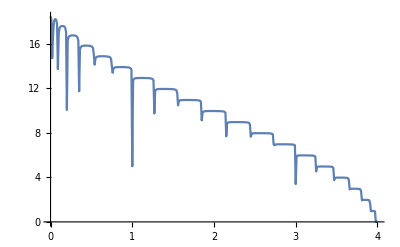

```mathematica
ListPlot[%429,Joined->True]
```

```mathematica
device2[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp,imp,imp,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[20]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[20]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[20]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/2imp.dat",%430]
```

/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/2imp.dat

```mathematica
Table[{ω,Mean[Table[device2[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,17.1297},{0.01,16.7216},{0.02,11.7294},{0.03,13.3284},{0.04,16.6548},{0.05,17.3033},{0.06,17.4749},{0.07,17.3195},{0.08,16.6918},{0.09,15.1727},{0.1,15.4952},{0.11,16.6878},{0.12,16.9984},{0.13,17.1388},{0.14,17.1849},{0.15,17.2028},{0.16,17.18},{0.17,17.1014},{0.18,16.9167},{0.19,16.3067},{0.2,11.8492},{0.21,15.3084},{0.22,16.1102},{0.23,16.3316},{0.24,16.4307},{0.25,16.4737},{0.26,16.5},{0.27,16.5045},{0.28,16.5109},{0.29,16.5044},{0.3,16.4805},{0.31,16.4328},{0.32,16.3546},{0.33,16.1872},{0.34,15.6432},{0.35,10.2409},{0.36,14.8127},{0.37,15.3593},{0.38,15.5174},{0.39,15.5883},{0.4,15.6264},{0.41,15.6456},{0.42,15.6584},{0.43,15.666},{0.44,15.6676},{0.45,15.6638},{0.46,15.6582},{0.47,15.6459},{0.48,15.6255},{0.49,15.5978},{0.5,15.5507},{0.51,15.4666},{0.52,15.2708},{0.53,14.3174},{0.54,12.3295},{0.55,14.3097},{0.56,14.5706},{0.57,14.6576},{0.58,14.6971},{0.59,14.7257},{0.6,14.7417},{0.61,14.7491},{0.62,14.7536},{0.63,14.7582},{0.64,14.7578},{0.65,14.7556},{0.66,14.753},{0.67,14.7459},{0.68,14.7376},{0.69,14.7251},{0.7,14.7062},{0.71,14.6766},{0.72,14.6365},{0.73,14.5609},{0.74,14.3678},{0.75,13.3452},{0.76,12.2536},{0.77,13.4769},{0.78,13.6635},{0.79,13.7343},{0.8,13.7645},{0.81,13.7867},{0.82,13.7982},{0.83,13.8064},{0.84,13.8094},{0.85,13.8127},{0.86,13.8155},{0.87,13.8146},{0.88,13.8134},{0.89,13.8121},{0.9,13.8077},{0.91,13.8021},{0.92,13.7947},{0.93,13.7847},{0.94,13.773},{0.95,13.7543},{0.96,13.7287},{0.97,13.6869},{0.98,13.5981},{0.99,13.3698},{1.,5.0876},{1.01,12.1718},{1.02,12.6484},{1.03,12.7493},{1.04,12.7932},{1.05,12.8196},{1.06,12.8334},{1.07,12.8416},{1.08,12.8463},{1.09,12.8496},{1.1,12.8525},{1.11,12.8533},{1.12,12.8535},{1.13,12.8537},{1.14,12.8518},{1.15,12.8491},{1.16,12.8474},{1.17,12.8431},{1.18,12.8368},{1.19,12.8308},{1.2,12.8226},{1.21,12.8111},{1.22,12.7942},{1.23,12.7693},{1.24,12.7319},{1.25,12.6526},{1.26,12.4353},{1.27,9.54094},{1.28,11.3439},{1.29,11.7115},{1.3,11.801},{1.31,11.8343},{1.32,11.8526},{1.33,11.8616},{1.34,11.8719},{1.35,11.876},{1.36,11.8781},{1.37,11.8801},{1.38,11.8809},{1.39,11.8814},{1.4,11.8809},{1.41,11.8804},{1.42,11.8781},{1.43,11.8767},{1.44,11.8744},{1.45,11.8713},{1.46,11.8678},{1.47,11.86},{1.48,11.8542},{1.49,11.8457},{1.5,11.8346},{1.51,11.8169},{1.52,11.7916},{1.53,11.7432},{1.54,11.6438},{1.55,11.2485},{1.56,9.07678},{1.57,10.6546},{1.58,10.798},{1.59,10.8463},{1.6,10.8685},{1.61,10.8807},{1.62,10.8885},{1.63,10.8942},{1.64,10.8971},{1.65,10.8992},{1.66,10.9009},{1.67,10.9013},{1.68,10.9008},{1.69,10.8999},{1.7,10.8995},{1.71,10.8981},{1.72,10.8967},{1.73,10.895},{1.74,10.892},{1.75,10.8893},{1.76,10.8845},{1.77,10.8803},{1.78,10.8737},{1.79,10.8645},{1.8,10.8513},{1.81,10.8336},{1.82,10.8078},{1.83,10.7501},{1.84,10.6103},{1.85,8.54159},{1.86,9.44312},{1.87,9.78364},{1.88,9.85483},{1.89,9.88066},{1.9,9.89448},{1.91,9.90221},{1.92,9.90768},{1.93,9.91159},{1.94,9.91377},{1.95,9.91378},{1.96,9.91538},{1.97,9.91606},{1.98,9.91695},{1.99,9.91565},{2.,9.91464},{2.01,9.91289},{2.02,9.91133},{2.03,9.90939},{2.04,9.90725},{2.05,9.9045},{2.06,9.90044},{2.07,9.89477},{2.08,9.88877},{2.09,9.88064},{2.1,9.86881},{2.11,9.85384},{2.12,9.82653},{2.13,9.77639},{2.14,9.62831},{2.15,6.63474},{2.16,8.58974},{2.17,8.82572},{2.18,8.87876},{2.19,8.90129},{2.2,8.91371},{2.21,8.91961},{2.22,8.92365},{2.23,8.92544},{2.24,8.92754},{2.25,8.92726},{2.26,8.92834},{2.27,8.92878},{2.28,8.9276},{2.29,8.92698},{2.3,8.927},{2.31,8.92499},{2.32,8.92354},{2.33,8.92091},{2.34,8.91884},{2.35,8.9157},{2.36,8.91176},{2.37,8.90658},{2.38,8.9011},{2.39,8.89294},{2.4,8.88024},{2.41,8.86106},{2.42,8.82982},{2.43,8.76651},{2.44,8.49508},{2.45,6.72448},{2.46,7.79145},{2.47,7.87773},{2.48,7.90807},{2.49,7.92091},{2.5,7.92817},{2.51,7.93258},{2.52,7.93416},{2.53,7.93598},{2.54,7.93704},{2.55,7.9365},{2.56,7.93757},{2.57,7.93665},{2.58,7.93575},{2.59,7.93554},{2.6,7.93466},{2.61,7.93295},{2.62,7.93045},{2.63,7.92814},{2.64,7.9249},{2.65,7.92103},{2.66,7.91641},{2.67,7.90904},{2.68,7.90074},{2.69,7.88968},{2.7,7.86858},{2.71,7.8296},{2.72,7.73696},{2.73,6.5066},{2.74,6.66},{2.75,6.8677},{2.76,6.90975},{2.77,6.92536},{2.78,6.93453},{2.79,6.93911},{2.8,6.94235},{2.81,6.94313},{2.82,6.94377},{2.83,6.94337},{2.84,6.94356},{2.85,6.94444},{2.86,6.94283},{2.87,6.94138},{2.88,6.94027},{2.89,6.93863},{2.9,6.93591},{2.91,6.93354},{2.92,6.92927},{2.93,6.92522},{2.94,6.91874},{2.95,6.91105},{2.96,6.89959},{2.97,6.88058},{2.98,6.84421},{2.99,6.75056},{3.,3.62759},{3.01,5.73978},{3.02,5.88736},{3.03,5.92276},{3.04,5.93607},{3.05,5.94156},{3.06,5.94603},{3.07,5.94766},{3.08,5.94866},{3.09,5.94952},{3.1,5.94969},{3.11,5.9483},{3.12,5.94792},{3.13,5.94651},{3.14,5.94439},{3.15,5.94269},{3.16,5.94011},{3.17,5.93634},{3.18,5.93199},{3.19,5.92718},{3.2,5.91769},{3.21,5.90626},{3.22,5.88418},{3.23,5.84568},{3.24,5.70556},{3.25,3.59813},{3.26,4.84891},{3.27,4.91709},{3.28,4.93672},{3.29,4.94452},{3.3,4.94951},{3.31,4.95185},{3.32,4.95341},{3.33,4.95345},{3.34,4.95294},{3.35,4.95123},{3.36,4.95023},{3.37,4.94919},{3.38,4.94681},{3.39,4.94268},{3.4,4.93876},{3.41,4.93429},{3.42,4.92567},{3.43,4.91363},{3.44,4.89456},{3.45,4.85268},{3.46,4.70705},{3.47,3.07183},{3.48,3.87993},{3.49,3.9309},{3.5,3.94586},{3.51,3.95154},{3.52,3.95475},{3.53,3.95561},{3.54,3.95564},{3.55,3.9552},{3.56,3.95347},{3.57,3.95112},{3.58,3.94819},{3.59,3.94485},{3.6,3.9387},{3.61,3.9302},{3.62,3.91646},{3.63,3.89463},{3.64,3.8422},{3.65,3.53287},{3.66,2.75709},{3.67,2.91757},{3.68,2.94547},{3.69,2.95371},{3.7,2.95699},{3.71,2.95658},{3.72,2.95683},{3.73,2.95372},{3.74,2.95058},{3.75,2.94546},{3.76,2.93736},{3.77,2.92692},{3.78,2.90366},{3.79,2.8519},{3.8,2.49835},{3.81,1.82634},{3.82,1.93433},{3.83,1.95116},{3.84,1.95577},{3.85,1.95465},{3.86,1.95197},{3.87,1.94501},{3.88,1.93324},{3.89,1.91181},{3.9,1.86029},{3.91,1.40885},{3.92,0.880228},{3.93,0.945356},{3.94,0.950503},{3.95,0.943918},{3.96,0.921689},{3.97,0.843198},{3.98,0.000455529},{3.99,0.0000167973},{4.,5.34586×10^-6}}

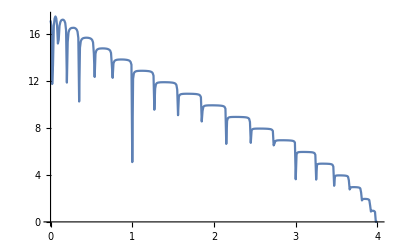

```mathematica
ListPlot[%430,Joined->True]
```

```mathematica
device3[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp4,imp5,imp,imp,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[20]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[20]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[20]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/3imp.dat",%431]
```

/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/3imp.dat

```mathematica
Table[{ω,Mean[Table[device3[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,16.0448},{0.01,15.5639},{0.02,10.2044},{0.03,10.3843},{0.04,15.3908},{0.05,16.4427},{0.06,16.7295},{0.07,16.594},{0.08,15.7984},{0.09,16.6635},{0.1,13.5211},{0.11,15.8748},{0.12,16.4551},{0.13,16.695},{0.14,16.7787},{0.15,16.8137},{0.16,16.8107},{0.17,16.6852},{0.18,16.4452},{0.19,15.7028},{0.2,14.3674},{0.21,13.9975},{0.22,15.5482},{0.23,15.9383},{0.24,16.1219},{0.25,16.2041},{0.26,16.2475},{0.27,16.2718},{0.28,16.2743},{0.29,16.2646},{0.3,16.2382},{0.31,16.1768},{0.32,16.0738},{0.33,15.858},{0.34,15.1856},{0.35,12.0261},{0.36,13.8241},{0.37,14.9614},{0.38,15.2321},{0.39,15.3686},{0.4,15.4346},{0.41,15.4749},{0.42,15.4901},{0.43,15.5004},{0.44,15.5046},{0.45,15.5074},{0.46,15.4926},{0.47,15.4751},{0.48,15.4537},{0.49,15.4153},{0.5,15.345},{0.51,15.2341},{0.52,14.9725},{0.53,13.8505},{0.54,9.60214},{0.55,13.7575},{0.56,14.2918},{0.57,14.4655},{0.58,14.5382},{0.59,14.5842},{0.6,14.6069},{0.61,14.6182},{0.62,14.6324},{0.63,14.6398},{0.64,14.6407},{0.65,14.6383},{0.66,14.6344},{0.67,14.6265},{0.68,14.6141},{0.69,14.5955},{0.7,14.5727},{0.71,14.5337},{0.72,14.4766},{0.73,14.3656},{0.74,14.137},{0.75,12.9284},{0.76,9.92267},{0.77,13.0872},{0.78,13.46},{0.79,13.5872},{0.8,13.6422},{0.81,13.6765},{0.82,13.6956},{0.83,13.7091},{0.84,13.7147},{0.85,13.7224},{0.86,13.725},{0.87,13.7267},{0.88,13.7253},{0.89,13.7221},{0.9,13.7143},{0.91,13.7093},{0.92,13.6981},{0.93,13.6864},{0.94,13.671},{0.95,13.6419},{0.96,13.6029},{0.97,13.5449},{0.98,13.4301},{0.99,13.131},{1.,6.60742},{1.01,11.2956},{1.02,12.3962},{1.03,12.6016},{1.04,12.684},{1.05,12.7237},{1.06,12.7458},{1.07,12.7641},{1.08,12.7718},{1.09,12.7768},{1.1,12.7822},{1.11,12.7814},{1.12,12.7832},{1.13,12.7834},{1.14,12.7817},{1.15,12.7794},{1.16,12.7754},{1.17,12.7688},{1.18,12.7615},{1.19,12.7527},{1.2,12.7412},{1.21,12.7257},{1.22,12.7014},{1.23,12.6664},{1.24,12.6089},{1.25,12.5055},{1.26,12.2205},{1.27,7.54208},{1.28,10.6917},{1.29,11.5095},{1.3,11.6815},{1.31,11.7438},{1.32,11.7731},{1.33,11.7942},{1.34,11.8059},{1.35,11.8149},{1.36,11.8193},{1.37,11.8222},{1.38,11.8247},{1.39,11.8239},{1.4,11.8243},{1.41,11.8239},{1.42,11.8221},{1.43,11.8191},{1.44,11.8148},{1.45,11.8105},{1.46,11.8062},{1.47,11.7967},{1.48,11.7878},{1.49,11.775},{1.5,11.7597},{1.51,11.7313},{1.52,11.6954},{1.53,11.6315},{1.54,11.4931},{1.55,10.995},{1.56,7.47082},{1.57,10.3634},{1.58,10.6757},{1.59,10.7571},{1.6,10.7989},{1.61,10.8203},{1.62,10.8335},{1.63,10.8424},{1.64,10.8477},{1.65,10.8504},{1.66,10.8528},{1.67,10.8539},{1.68,10.8544},{1.69,10.8544},{1.7,10.8515},{1.71,10.8522},{1.72,10.849},{1.73,10.8445},{1.74,10.8415},{1.75,10.8387},{1.76,10.831},{1.77,10.8253},{1.78,10.8146},{1.79,10.8003},{1.8,10.782},{1.81,10.7587},{1.82,10.717},{1.83,10.6363},{1.84,10.4482},{1.85,8.46545},{1.86,8.80868},{1.87,9.63188},{1.88,9.76196},{1.89,9.81609},{1.9,9.84029},{1.91,9.85471},{1.92,9.86427},{1.93,9.8681},{1.94,9.87204},{1.95,9.87508},{1.96,9.87685},{1.97,9.87696},{1.98,9.87578},{1.99,9.875},{2.,9.8751},{2.01,9.87352},{2.02,9.87189},{2.03,9.86791},{2.04,9.86362},{2.05,9.86031},{2.06,9.85332},{2.07,9.84802},{2.08,9.83643},{2.09,9.82468},{2.1,9.80809},{2.11,9.78346},{2.12,9.74288},{2.13,9.67113},{2.14,9.47852},{2.15,5.55098},{2.16,8.16781},{2.17,8.70956},{2.18,8.80813},{2.19,8.84803},{2.2,8.86742},{2.21,8.8775},{2.22,8.88547},{2.23,8.88903},{2.24,8.89192},{2.25,8.89342},{2.26,8.8942},{2.27,8.89471},{2.28,8.89489},{2.29,8.89324},{2.3,8.89253},{2.31,8.8911},{2.32,8.88782},{2.33,8.88501},{2.34,8.88083},{2.35,8.87708},{2.36,8.87106},{2.37,8.8655},{2.38,8.85502},{2.39,8.84036},{2.4,8.82273},{2.41,8.79825},{2.42,8.7515},{2.43,8.65948},{2.44,8.30758},{2.45,5.68277},{2.46,7.61282},{2.47,7.80054},{2.48,7.85589},{2.49,7.87861},{2.5,7.89033},{2.51,7.89793},{2.52,7.90287},{2.53,7.90582},{2.54,7.90688},{2.55,7.90814},{2.56,7.90877},{2.57,7.90752},{2.58,7.90632},{2.59,7.90607},{2.6,7.90377},{2.61,7.90189},{2.62,7.89874},{2.63,7.89454},{2.64,7.89108},{2.65,7.88405},{2.66,7.87721},{2.67,7.86798},{2.68,7.85529},{2.69,7.83578},{2.7,7.80299},{2.71,7.75014},{2.72,7.61505},{2.73,6.35704},{2.74,6.2322},{2.75,6.77255},{2.76,6.85454},{2.77,6.88601},{2.78,6.90152},{2.79,6.90913},{2.8,6.91355},{2.81,6.91599},{2.82,6.91723},{2.83,6.91763},{2.84,6.91831},{2.85,6.91828},{2.86,6.91665},{2.87,6.91509},{2.88,6.91365},{2.89,6.91004},{2.9,6.90751},{2.91,6.90297},{2.92,6.89684},{2.93,6.89149},{2.94,6.88069},{2.95,6.86908},{2.96,6.85082},{2.97,6.82269},{2.98,6.76861},{2.99,6.6302},{3.,4.23065},{3.01,5.45568},{3.02,5.81172},{3.03,5.87947},{3.04,5.90164},{3.05,5.91323},{3.06,5.91945},{3.07,5.92328},{3.08,5.92475},{3.09,5.92639},{3.1,5.92545},{3.11,5.9257},{3.12,5.92398},{3.13,5.92269},{3.14,5.91951},{3.15,5.91655},{3.16,5.9124},{3.17,5.90792},{3.18,5.90024},{3.19,5.89031},{3.2,5.87847},{3.21,5.85897},{3.22,5.82898},{3.23,5.76649},{3.24,5.5887},{3.25,3.79741},{3.26,4.68887},{3.27,4.86132},{3.28,4.90182},{3.29,4.91734},{3.3,4.92538},{3.31,4.92911},{3.32,4.93153},{3.33,4.93165},{3.34,4.93082},{3.35,4.93003},{3.36,4.92854},{3.37,4.92556},{3.38,4.92217},{3.39,4.91706},{3.4,4.91144},{3.41,4.90092},{3.42,4.89022},{3.43,4.87186},{3.44,4.83995},{3.45,4.78031},{3.46,4.58157},{3.47,2.88335},{3.48,3.77135},{3.49,3.8878},{3.5,3.9169},{3.51,3.92735},{3.52,3.93391},{3.53,3.93431},{3.54,3.93492},{3.55,3.93402},{3.56,3.93166},{3.57,3.92854},{3.58,3.92361},{3.59,3.91773},{3.6,3.90896},{3.61,3.89624},{3.62,3.87576},{3.63,3.83932},{3.64,3.7583},{3.65,3.36056},{3.66,2.41097},{3.67,2.86433},{3.68,2.91454},{3.69,2.93083},{3.7,2.93478},{3.71,2.93633},{3.72,2.934},{3.73,2.93205},{3.74,2.9258},{3.75,2.9167},{3.76,2.9069},{3.77,2.88656},{3.78,2.85084},{3.79,2.77254},{3.8,2.33414},{3.81,1.58307},{3.82,1.88918},{3.83,1.92346},{3.84,1.9296},{3.85,1.93067},{3.86,1.92458},{3.87,1.91286},{3.88,1.89455},{3.89,1.86148},{3.9,1.77983},{3.91,1.23047},{3.92,0.764461},{3.93,0.902319},{3.94,0.917184},{3.95,0.904043},{3.96,0.867371},{3.97,0.749176},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

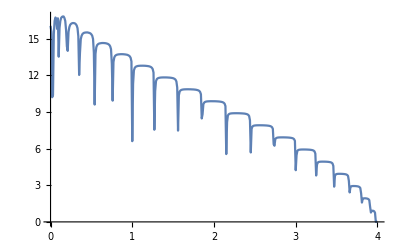

```mathematica
ListPlot[%431,Joined->True]
```

```mathematica
device4[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp4,imp5,imp,imp7,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[20]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[20]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[20]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/4imp.dat",%432]
```

/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/4imp.dat

```mathematica
Table[{ω,Mean[Table[device4[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,15.0854},{0.01,14.6643},{0.02,9.58797},{0.03,9.57485},{0.04,13.8207},{0.05,15.5094},{0.06,15.9425},{0.07,15.9188},{0.08,15.0911},{0.09,15.8525},{0.1,10.9386},{0.11,14.8244},{0.12,15.8623},{0.13,16.1876},{0.14,16.3636},{0.15,16.4343},{0.16,16.3998},{0.17,16.3059},{0.18,16.0344},{0.19,15.2163},{0.2,14.9494},{0.21,11.9433},{0.22,14.8565},{0.23,15.5333},{0.24,15.8059},{0.25,15.925},{0.26,15.9896},{0.27,16.026},{0.28,16.0381},{0.29,16.0306},{0.3,15.988},{0.31,15.9379},{0.32,15.8088},{0.33,15.5583},{0.34,14.8194},{0.35,13.3041},{0.36,12.2847},{0.37,14.4608},{0.38,14.9466},{0.39,15.1253},{0.4,15.2189},{0.41,15.2931},{0.42,15.3117},{0.43,15.3388},{0.44,15.3502},{0.45,15.3473},{0.46,15.3399},{0.47,15.3144},{0.48,15.2897},{0.49,15.2323},{0.5,15.1691},{0.51,15.0261},{0.52,14.7331},{0.53,13.5466},{0.54,8.97235},{0.55,13.0048},{0.56,13.9511},{0.57,14.251},{0.58,14.3705},{0.59,14.4383},{0.6,14.4678},{0.61,14.4984},{0.62,14.5131},{0.63,14.5245},{0.64,14.5268},{0.65,14.5248},{0.66,14.5202},{0.67,14.5085},{0.68,14.4925},{0.69,14.4751},{0.7,14.4408},{0.71,14.3907},{0.72,14.325},{0.73,14.1942},{0.74,13.912},{0.75,12.6799},{0.76,8.47902},{0.77,12.5467},{0.78,13.2105},{0.79,13.4143},{0.8,13.5109},{0.81,13.5628},{0.82,13.5922},{0.83,13.6139},{0.84,13.6252},{0.85,13.6328},{0.86,13.6368},{0.87,13.6415},{0.88,13.6381},{0.89,13.6325},{0.9,13.6279},{0.91,13.621},{0.92,13.6065},{0.93,13.5884},{0.94,13.5658},{0.95,13.5332},{0.96,13.4883},{0.97,13.4097},{0.98,13.2733},{0.99,12.9311},{1.,8.00811},{1.01,9.55924},{1.02,12.0726},{1.03,12.4208},{1.04,12.5615},{1.05,12.6232},{1.06,12.6599},{1.07,12.6814},{1.08,12.695},{1.09,12.704},{1.1,12.7091},{1.11,12.7139},{1.12,12.7173},{1.13,12.7174},{1.14,12.7125},{1.15,12.7073},{1.16,12.7043},{1.17,12.6988},{1.18,12.6908},{1.19,12.6766},{1.2,12.6615},{1.21,12.6396},{1.22,12.6101},{1.23,12.5622},{1.24,12.4993},{1.25,12.3668},{1.26,12.0417},{1.27,6.61605},{1.28,9.4722},{1.29,11.2445},{1.3,11.5356},{1.31,11.6422},{1.32,11.6951},{1.33,11.7231},{1.34,11.74},{1.35,11.7549},{1.36,11.7601},{1.37,11.765},{1.38,11.7669},{1.39,11.7702},{1.4,11.7699},{1.41,11.7704},{1.42,11.7665},{1.43,11.7623},{1.44,11.758},{1.45,11.754},{1.46,11.7455},{1.47,11.7371},{1.48,11.7201},{1.49,11.7049},{1.5,11.682},{1.51,11.6536},{1.52,11.6069},{1.53,11.5291},{1.54,11.3638},{1.55,10.8103},{1.56,7.4365},{1.57,9.90701},{1.58,10.5099},{1.59,10.6582},{1.6,10.7266},{1.61,10.7559},{1.62,10.7772},{1.63,10.7879},{1.64,10.7972},{1.65,10.8033},{1.66,10.807},{1.67,10.8077},{1.68,10.8092},{1.69,10.8106},{1.7,10.8077},{1.71,10.8068},{1.72,10.8024},{1.73,10.7988},{1.74,10.7934},{1.75,10.787},{1.76,10.7781},{1.77,10.7703},{1.78,10.7578},{1.79,10.7372},{1.8,10.7198},{1.81,10.6835},{1.82,10.6309},{1.83,10.5364},{1.84,10.3087},{1.85,8.53403},{1.86,7.47877},{1.87,9.40997},{1.88,9.65894},{1.89,9.73775},{1.9,9.78215},{1.91,9.80425},{1.92,9.81893},{1.93,9.82524},{1.94,9.83105},{1.95,9.83634},{1.96,9.83701},{1.97,9.83645},{1.98,9.83893},{1.99,9.83714},{2.,9.83618},{2.01,9.83529},{2.02,9.8315},{2.03,9.82737},{2.04,9.82218},{2.05,9.81693},{2.06,9.80813},{2.07,9.80137},{2.08,9.78831},{2.09,9.77056},{2.1,9.752},{2.11,9.71908},{2.12,9.667},{2.13,9.57718},{2.14,9.34231},{2.15,5.20103},{2.16,7.24977},{2.17,8.52375},{2.18,8.72113},{2.19,8.78951},{2.2,8.81909},{2.21,8.83698},{2.22,8.8478},{2.23,8.85396},{2.24,8.85802},{2.25,8.86114},{2.26,8.86212},{2.27,8.86261},{2.28,8.86235},{2.29,8.86115},{2.3,8.85995},{2.31,8.85906},{2.32,8.85591},{2.33,8.85061},{2.34,8.84673},{2.35,8.83999},{2.36,8.83155},{2.37,8.82322},{2.38,8.80989},{2.39,8.79279},{2.4,8.77004},{2.41,8.73349},{2.42,8.67684},{2.43,8.56044},{2.44,8.15431},{2.45,5.59034},{2.46,7.32497},{2.47,7.69975},{2.48,7.79485},{2.49,7.834},{2.5,7.85285},{2.51,7.86586},{2.52,7.87233},{2.53,7.87669},{2.54,7.8788},{2.55,7.88094},{2.56,7.88133},{2.57,7.88093},{2.58,7.87919},{2.59,7.87841},{2.6,7.87494},{2.61,7.87215},{2.62,7.86947},{2.63,7.86428},{2.64,7.85804},{2.65,7.85002},{2.66,7.84199},{2.67,7.82764},{2.68,7.80975},{2.69,7.78271},{2.7,7.74435},{2.71,7.67403},{2.72,7.50686},{2.73,6.34483},{2.74,5.41968},{2.75,6.63047},{2.76,6.7907},{2.77,6.84032},{2.78,6.86512},{2.79,6.87788},{2.8,6.8856},{2.81,6.88997},{2.82,6.8928},{2.83,6.89354},{2.84,6.89407},{2.85,6.89335},{2.86,6.89156},{2.87,6.8902},{2.88,6.88701},{2.89,6.88421},{2.9,6.87869},{2.91,6.87337},{2.92,6.86744},{2.93,6.85579},{2.94,6.84602},{2.95,6.82726},{2.96,6.80575},{2.97,6.76514},{2.98,6.6967},{2.99,6.53647},{3.,4.62121},{3.01,4.78958},{3.02,5.7136},{3.03,5.82663},{3.04,5.86741},{3.05,5.8837},{3.06,5.89449},{3.07,5.89963},{3.08,5.90223},{3.09,5.90391},{3.1,5.90393},{3.11,5.90189},{3.12,5.90113},{3.13,5.89951},{3.14,5.89649},{3.15,5.89087},{3.16,5.88657},{3.17,5.87906},{3.18,5.87024},{3.19,5.85756},{3.2,5.84029},{3.21,5.81415},{3.22,5.77551},{3.23,5.692},{3.24,5.47435},{3.25,3.71799},{3.26,4.44376},{3.27,4.7923},{3.28,4.86043},{3.29,4.88853},{3.3,4.90114},{3.31,4.90743},{3.32,4.90911},{3.33,4.9111},{3.34,4.91071},{3.35,4.90941},{3.36,4.90653},{3.37,4.90421},{3.38,4.89782},{3.39,4.8918},{3.4,4.88325},{3.41,4.87253},{3.42,4.85535},{3.43,4.82903},{3.44,4.79025},{3.45,4.71067},{3.46,4.46934},{3.47,2.9574},{3.48,3.58049},{3.49,3.83514},{3.5,3.88299},{3.51,3.90252},{3.52,3.91178},{3.53,3.91586},{3.54,3.91708},{3.55,3.91507},{3.56,3.91291},{3.57,3.90716},{3.58,3.89952},{3.59,3.89263},{3.6,3.88085},{3.61,3.86025},{3.62,3.83698},{3.63,3.789},{3.64,3.68024},{3.65,3.23916},{3.66,2.12574},{3.67,2.78594},{3.68,2.87906},{3.69,2.90517},{3.7,2.91393},{3.71,2.91612},{3.72,2.91471},{3.73,2.91071},{3.74,2.90348},{3.75,2.89074},{3.76,2.87298},{3.77,2.84661},{3.78,2.79725},{3.79,2.69855},{3.8,2.22288},{3.81,1.40167},{3.82,1.82467},{3.83,1.89016},{3.84,1.90421},{3.85,1.90504},{3.86,1.89492},{3.87,1.88162},{3.88,1.85732},{3.89,1.80569},{3.9,1.69649},{3.91,1.12743},{3.92,0.666941},{3.93,0.844487},{3.94,0.876457},{3.95,0.860892},{3.96,0.811008},{3.97,0.655404},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

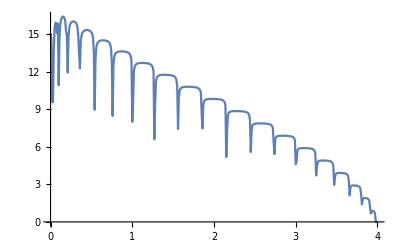

```mathematica
ListPlot[%432,Joined->True]
```

```mathematica
device5[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,20}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{1,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp4,imp5,imp8,imp7,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[20]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[20]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[20]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/5imp.dat",%433]
```

/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/5imp.dat

```mathematica
Table[{ω,Mean[Table[device5[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,14.3581},{0.01,13.8456},{0.02,9.15863},{0.03,10.5807},{0.04,11.9473},{0.05,14.5145},{0.06,15.235},{0.07,15.3014},{0.08,14.4922},{0.09,13.5605},{0.1,8.90157},{0.11,13.672},{0.12,15.1373},{0.13,15.6945},{0.14,15.9505},{0.15,16.0327},{0.16,16.0667},{0.17,15.9579},{0.18,15.6571},{0.19,14.8149},{0.2,13.255},{0.21,9.61387},{0.22,14.0021},{0.23,15.007},{0.24,15.4488},{0.25,15.6202},{0.26,15.7404},{0.27,15.7869},{0.28,15.807},{0.29,15.8004},{0.3,15.7688},{0.31,15.7033},{0.32,15.561},{0.33,15.2813},{0.34,14.52},{0.35,12.3066},{0.36,10.088},{0.37,13.771},{0.38,14.5395},{0.39,14.8667},{0.4,15.0178},{0.41,15.0991},{0.42,15.1428},{0.43,15.1727},{0.44,15.1836},{0.45,15.1937},{0.46,15.1906},{0.47,15.1726},{0.48,15.1251},{0.49,15.0764},{0.5,14.98},{0.51,14.8365},{0.52,14.5025},{0.53,13.339},{0.54,9.82456},{0.55,11.9061},{0.56,13.5705},{0.57,14.0092},{0.58,14.1816},{0.59,14.2888},{0.6,14.3393},{0.61,14.3705},{0.62,14.395},{0.63,14.4055},{0.64,14.4103},{0.65,14.4095},{0.66,14.4073},{0.67,14.3968},{0.68,14.3807},{0.69,14.3524},{0.7,14.3169},{0.71,14.2678},{0.72,14.1778},{0.73,14.0369},{0.74,13.7316},{0.75,12.538},{0.76,8.71492},{0.77,11.7108},{0.78,12.8978},{0.79,13.2274},{0.8,13.3675},{0.81,13.4422},{0.82,13.4892},{0.83,13.5186},{0.84,13.533},{0.85,13.5445},{0.86,13.5481},{0.87,13.5501},{0.88,13.5497},{0.89,13.547},{0.9,13.5428},{0.91,13.533},{0.92,13.5167},{0.93,13.4953},{0.94,13.4687},{0.95,13.4356},{0.96,13.3772},{0.97,13.292},{0.98,13.1328},{0.99,12.7772},{1.,8.95855},{1.01,8.03681},{1.02,11.5608},{1.03,12.2154},{1.04,12.416},{1.05,12.5176},{1.06,12.5666},{1.07,12.5985},{1.08,12.6176},{1.09,12.633},{1.1,12.6415},{1.11,12.6478},{1.12,12.6505},{1.13,12.6489},{1.14,12.6486},{1.15,12.6419},{1.16,12.6379},{1.17,12.6293},{1.18,12.6202},{1.19,12.6069},{1.2,12.5859},{1.21,12.5577},{1.22,12.5218},{1.23,12.4706},{1.24,12.398},{1.25,12.2557},{1.26,11.888},{1.27,6.65887},{1.28,7.86023},{1.29,10.8554},{1.3,11.3603},{1.31,11.5324},{1.32,11.6053},{1.33,11.6508},{1.34,11.6746},{1.35,11.691},{1.36,11.7033},{1.37,11.7104},{1.38,11.7142},{1.39,11.7155},{1.4,11.7163},{1.41,11.7161},{1.42,11.7122},{1.43,11.7079},{1.44,11.7035},{1.45,11.6985},{1.46,11.6904},{1.47,11.6768},{1.48,11.6625},{1.49,11.6439},{1.5,11.6123},{1.51,11.5798},{1.52,11.5234},{1.53,11.4319},{1.54,11.2482},{1.55,10.6822},{1.56,8.01385},{1.57,9.16373},{1.58,10.3053},{1.59,10.5432},{1.6,10.641},{1.61,10.695},{1.62,10.7218},{1.63,10.7381},{1.64,10.749},{1.65,10.7558},{1.66,10.7608},{1.67,10.7632},{1.68,10.7637},{1.69,10.7666},{1.7,10.7641},{1.71,10.7634},{1.72,10.7586},{1.73,10.7524},{1.74,10.7504},{1.75,10.7403},{1.76,10.7306},{1.77,10.7199},{1.78,10.7045},{1.79,10.6845},{1.8,10.6561},{1.81,10.617},{1.82,10.5515},{1.83,10.4429},{1.84,10.2001},{1.85,8.65598},{1.86,6.44379},{1.87,9.08495},{1.88,9.52619},{1.89,9.6607},{1.9,9.72436},{1.91,9.75143},{1.92,9.77296},{1.93,9.78407},{1.94,9.79188},{1.95,9.79766},{1.96,9.80142},{1.97,9.80122},{1.98,9.80161},{1.99,9.80236},{2.,9.79996},{2.01,9.79807},{2.02,9.79221},{2.03,9.78939},{2.04,9.78319},{2.05,9.77652},{2.06,9.76846},{2.07,9.75653},{2.08,9.74224},{2.09,9.72143},{2.1,9.69556},{2.11,9.65648},{2.12,9.59537},{2.13,9.4918},{2.14,9.23564},{2.15,5.92398},{2.16,6.36766},{2.17,8.30371},{2.18,8.6144},{2.19,8.72326},{2.2,8.76856},{2.21,8.79558},{2.22,8.8095},{2.23,8.81835},{2.24,8.82581},{2.25,8.82988},{2.26,8.83156},{2.27,8.83211},{2.28,8.8321},{2.29,8.83125},{2.3,8.83032},{2.31,8.8272},{2.32,8.82313},{2.33,8.82044},{2.34,8.81151},{2.35,8.80436},{2.36,8.79508},{2.37,8.78319},{2.38,8.76864},{2.39,8.75059},{2.4,8.7195},{2.41,8.67894},{2.42,8.60894},{2.43,8.47281},{2.44,8.0532},{2.45,5.74543},{2.46,6.76332},{2.47,7.57757},{2.48,7.72766},{2.49,7.78617},{2.5,7.81626},{2.51,7.8318},{2.52,7.84153},{2.53,7.84779},{2.54,7.85072},{2.55,7.85425},{2.56,7.85397},{2.57,7.85541},{2.58,7.85259},{2.59,7.85082},{2.6,7.8482},{2.61,7.84586},{2.62,7.83953},{2.63,7.83402},{2.64,7.82742},{2.65,7.8162},{2.66,7.80571},{2.67,7.78901},{2.68,7.76761},{2.69,7.73892},{2.7,7.68902},{2.71,7.60534},{2.72,7.41665},{2.73,6.35888},{2.74,4.84995},{2.75,6.42875},{2.76,6.71414},{2.77,6.79448},{2.78,6.82981},{2.79,6.84752},{2.8,6.85801},{2.81,6.86499},{2.82,6.86803},{2.83,6.87067},{2.84,6.87142},{2.85,6.87113},{2.86,6.87003},{2.87,6.8675},{2.88,6.86342},{2.89,6.85889},{2.9,6.85255},{2.91,6.84591},{2.92,6.83777},{2.93,6.82452},{2.94,6.8115},{2.95,6.79065},{2.96,6.76057},{2.97,6.71148},{2.98,6.6343},{2.99,6.44477},{3.,4.98096},{3.01,4.30315},{3.02,5.55147},{3.03,5.76143},{3.04,5.82616},{3.05,5.85435},{3.06,5.86688},{3.07,5.87582},{3.08,5.88103},{3.09,5.88323},{3.1,5.88204},{3.11,5.88153},{3.12,5.88024},{3.13,5.87763},{3.14,5.87344},{3.15,5.86798},{3.16,5.86116},{3.17,5.85297},{3.18,5.8407},{3.19,5.82584},{3.2,5.80564},{3.21,5.77193},{3.22,5.72241},{3.23,5.62703},{3.24,5.37932},{3.25,3.34651},{3.26,3.95454},{3.27,4.692},{3.28,4.81379},{3.29,4.85707},{3.3,4.87608},{3.31,4.88504},{3.32,4.88949},{3.33,4.8933},{3.34,4.89213},{3.35,4.89079},{3.36,4.88755},{3.37,4.88286},{3.38,4.87582},{3.39,4.86821},{3.4,4.85727},{3.41,4.84278},{3.42,4.82026},{3.43,4.7935},{3.44,4.74246},{3.45,4.64756},{3.46,4.37902},{3.47,2.86906},{3.48,3.24646},{3.49,3.75801},{3.5,3.8492},{3.51,3.87595},{3.52,3.89166},{3.53,3.89636},{3.54,3.89821},{3.55,3.89709},{3.56,3.89345},{3.57,3.8889},{3.58,3.87962},{3.59,3.86872},{3.6,3.85302},{3.61,3.83207},{3.62,3.79694},{3.63,3.73598},{3.64,3.61359},{3.65,3.15204},{3.66,2.13328},{3.67,2.64114},{3.68,2.83366},{3.69,2.87914},{3.7,2.89277},{3.71,2.89644},{3.72,2.89558},{3.73,2.88917},{3.74,2.87874},{3.75,2.86589},{3.76,2.84229},{3.77,2.80736},{3.78,2.74899},{3.79,2.62245},{3.8,2.12948},{3.81,1.40893},{3.82,1.71563},{3.83,1.84911},{3.84,1.87644},{3.85,1.87924},{3.86,1.86873},{3.87,1.84778},{3.88,1.8131},{3.89,1.75307},{3.9,1.62502},{3.91,1.05194},{3.92,0.692869},{3.93,0.768265},{3.94,0.831456},{3.95,0.816213},{3.96,0.754004},{3.97,0.570288},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

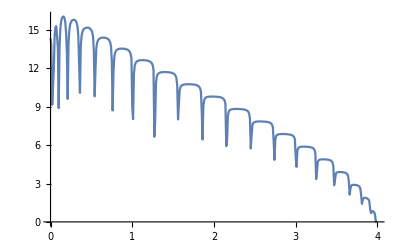

```mathematica
ListPlot[%433,Joined->True]
```

```mathematica
device6[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,10}], μ2=RandomInteger[{1,20}], μ3=RandomInteger[{11,20}], μ4=RandomInteger[{1,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp4,imp5,imp8,imp7,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[20]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[20]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[20]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/6imp.dat",%435]
```

/home/shardulmukim/PhD/fwi/sq_lattice/20sq/5unit/6imp.dat

```mathematica
Table[{ω,Mean[Table[device6[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,13.7062},{0.01,13.0669},{0.02,9.15621},{0.03,12.8299},{0.04,10.1351},{0.05,13.3475},{0.06,14.3993},{0.07,14.6794},{0.08,13.9005},{0.09,11.4466},{0.1,8.38695},{0.11,12.3063},{0.12,14.3968},{0.13,15.167},{0.14,15.5117},{0.15,15.6568},{0.16,15.6849},{0.17,15.5993},{0.18,15.3101},{0.19,14.5147},{0.2,10.5625},{0.21,8.38662},{0.22,12.8649},{0.23,14.4621},{0.24,15.0357},{0.25,15.3112},{0.26,15.4577},{0.27,15.5311},{0.28,15.5788},{0.29,15.5809},{0.3,15.5576},{0.31,15.4737},{0.32,15.3392},{0.33,15.0554},{0.34,14.2671},{0.35,10.1683},{0.36,8.64165},{0.37,12.869},{0.38,14.1536},{0.39,14.5839},{0.4,14.7936},{0.41,14.902},{0.42,14.9828},{0.43,15.0134},{0.44,15.0305},{0.45,15.0388},{0.46,15.0325},{0.47,15.017},{0.48,14.9722},{0.49,14.9193},{0.5,14.8189},{0.51,14.6526},{0.52,14.3082},{0.53,13.1879},{0.54,11.0954},{0.55,10.3014},{0.56,13.0467},{0.57,13.7187},{0.58,13.9897},{0.59,14.1148},{0.6,14.1935},{0.61,14.2478},{0.62,14.2704},{0.63,14.2918},{0.64,14.2975},{0.65,14.2983},{0.66,14.2906},{0.67,14.2816},{0.68,14.2703},{0.69,14.2366},{0.7,14.1997},{0.71,14.1409},{0.72,14.0461},{0.73,13.8945},{0.74,13.572},{0.75,12.436},{0.76,9.69119},{0.77,10.3075},{0.78,12.4997},{0.79,12.99},{0.8,13.2117},{0.81,13.3204},{0.82,13.3808},{0.83,13.4155},{0.84,13.44},{0.85,13.4547},{0.86,13.4595},{0.87,13.4718},{0.88,13.4699},{0.89,13.4658},{0.9,13.4578},{0.91,13.448},{0.92,13.4318},{0.93,13.4083},{0.94,13.3815},{0.95,13.3357},{0.96,13.2794},{0.97,13.1816},{0.98,13.0182},{0.99,12.6343},{1.,9.65101},{1.01,7.84396},{1.02,10.8771},{1.03,11.9305},{1.04,12.2514},{1.05,12.3943},{1.06,12.4698},{1.07,12.5137},{1.08,12.541},{1.09,12.5614},{1.1,12.5677},{1.11,12.5791},{1.12,12.5807},{1.13,12.5833},{1.14,12.5802},{1.15,12.5781},{1.16,12.5707},{1.17,12.5625},{1.18,12.5469},{1.19,12.5338},{1.2,12.5103},{1.21,12.4837},{1.22,12.4419},{1.23,12.3904},{1.24,12.2964},{1.25,12.1383},{1.26,11.7804},{1.27,7.30292},{1.28,7.26937},{1.29,10.2922},{1.3,11.1591},{1.31,11.4019},{1.32,11.5147},{1.33,11.575},{1.34,11.6043},{1.35,11.6281},{1.36,11.6429},{1.37,11.6536},{1.38,11.6591},{1.39,11.6627},{1.4,11.6622},{1.41,11.6631},{1.42,11.6618},{1.43,11.6581},{1.44,11.6507},{1.45,11.6441},{1.46,11.6349},{1.47,11.6204},{1.48,11.5996},{1.49,11.576},{1.5,11.5469},{1.51,11.5061},{1.52,11.445},{1.53,11.346},{1.54,11.1517},{1.55,10.5842},{1.56,7.77252},{1.57,7.93004},{1.58,10.002},{1.59,10.3972},{1.6,10.5552},{1.61,10.6199},{1.62,10.6582},{1.63,10.6826},{1.64,10.6999},{1.65,10.709},{1.66,10.7156},{1.67,10.7184},{1.68,10.7198},{1.69,10.7224},{1.7,10.7216},{1.71,10.7159},{1.72,10.7153},{1.73,10.709},{1.74,10.7024},{1.75,10.6944},{1.76,10.6824},{1.77,10.6682},{1.78,10.6498},{1.79,10.6263},{1.8,10.5968},{1.81,10.5511},{1.82,10.4793},{1.83,10.358},{1.84,10.1031},{1.85,8.76367},{1.86,6.38063},{1.87,8.59812},{1.88,9.36414},{1.89,9.56998},{1.9,9.65006},{1.91,9.69652},{1.92,9.72386},{1.93,9.74076},{1.94,9.7488},{1.95,9.75765},{1.96,9.76177},{1.97,9.76652},{1.98,9.76566},{1.99,9.76649},{2.,9.76587},{2.01,9.76212},{2.02,9.75766},{2.03,9.75072},{2.04,9.74632},{2.05,9.73838},{2.06,9.7264},{2.07,9.71178},{2.08,9.69492},{2.09,9.67504},{2.1,9.64303},{2.11,9.59901},{2.12,9.53155},{2.13,9.413},{2.14,9.14579},{2.15,6.47612},{2.16,5.98833},{2.17,7.90427},{2.18,8.48419},{2.19,8.65039},{2.2,8.71087},{2.21,8.74896},{2.22,8.76848},{2.23,8.7829},{2.24,8.79135},{2.25,8.79697},{2.26,8.79911},{2.27,8.80167},{2.28,8.80217},{2.29,8.80067},{2.3,8.79798},{2.31,8.79656},{2.32,8.79014},{2.33,8.78438},{2.34,8.77775},{2.35,8.77097},{2.36,8.7581},{2.37,8.74497},{2.38,8.72947},{2.39,8.70289},{2.4,8.67056},{2.41,8.62441},{2.42,8.54325},{2.43,8.3921},{2.44,7.96767},{2.45,5.60437},{2.46,5.98961},{2.47,7.37143},{2.48,7.64645},{2.49,7.73112},{2.5,7.7727},{2.51,7.79682},{2.52,7.80997},{2.53,7.8182},{2.54,7.82221},{2.55,7.82668},{2.56,7.82857},{2.57,7.82783},{2.58,7.82797},{2.59,7.82614},{2.6,7.82049},{2.61,7.81876},{2.62,7.81219},{2.63,7.80436},{2.64,7.79612},{2.65,7.7824},{2.66,7.77003},{2.67,7.75331},{2.68,7.72698},{2.69,7.68991},{2.7,7.63468},{2.71,7.53816},{2.72,7.34191},{2.73,6.3985},{2.74,4.72151},{2.75,6.05419},{2.76,6.60575},{2.77,6.73883},{2.78,6.78755},{2.79,6.81503},{2.8,6.82963},{2.81,6.83867},{2.82,6.84408},{2.83,6.84736},{2.84,6.84761},{2.85,6.84675},{2.86,6.84518},{2.87,6.84247},{2.88,6.83813},{2.89,6.83368},{2.9,6.8271},{2.91,6.81925},{2.92,6.80697},{2.93,6.79526},{2.94,6.77558},{2.95,6.75179},{2.96,6.71798},{2.97,6.66399},{2.98,6.57245},{2.99,6.36576},{3.,5.16153},{3.01,4.35639},{3.02,5.28409},{3.03,5.68309},{3.04,5.783},{3.05,5.82076},{3.06,5.84092},{3.07,5.85108},{3.08,5.85785},{3.09,5.86073},{3.1,5.86178},{3.11,5.86139},{3.12,5.85984},{3.13,5.85798},{3.14,5.85075},{3.15,5.8458},{3.16,5.83557},{3.17,5.82501},{3.18,5.81102},{3.19,5.7926},{3.2,5.77052},{3.21,5.73101},{3.22,5.67356},{3.23,5.56887},{3.24,5.30261},{3.25,3.19648},{3.26,3.54365},{3.27,4.54815},{3.28,4.75681},{3.29,4.82223},{3.3,4.8497},{3.31,4.86281},{3.32,4.86808},{3.33,4.87248},{3.34,4.8722},{3.35,4.87054},{3.36,4.86745},{3.37,4.8621},{3.38,4.8536},{3.39,4.84407},{3.4,4.8307},{3.41,4.81086},{3.42,4.78781},{3.43,4.75029},{3.44,4.69269},{3.45,4.59193},{3.46,4.30711},{3.47,2.6456},{3.48,2.92068},{3.49,3.66273},{3.5,3.79858},{3.51,3.84786},{3.52,3.86773},{3.53,3.87695},{3.54,3.87935},{3.55,3.87763},{3.56,3.87564},{3.57,3.86823},{3.58,3.85872},{3.59,3.84337},{3.6,3.82687},{3.61,3.79569},{3.62,3.75968},{3.63,3.68796},{3.64,3.54763},{3.65,3.09278},{3.66,2.1578},{3.67,2.42008},{3.68,2.78142},{3.69,2.85098},{3.7,2.86896},{3.71,2.87774},{3.72,2.87603},{3.73,2.86834},{3.74,2.85722},{3.75,2.83766},{3.76,2.81171},{3.77,2.77152},{3.78,2.69942},{3.79,2.55803},{3.8,2.08334},{3.81,1.47146},{3.82,1.57088},{3.83,1.80278},{3.84,1.84541},{3.85,1.85204},{3.86,1.83982},{3.87,1.81578},{3.88,1.77516},{3.89,1.70458},{3.9,1.55514},{3.91,1.01477},{3.92,0.743774},{3.93,0.700779},{3.94,0.794786},{3.95,0.77768},{3.96,0.701729},{3.97,0.506567},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

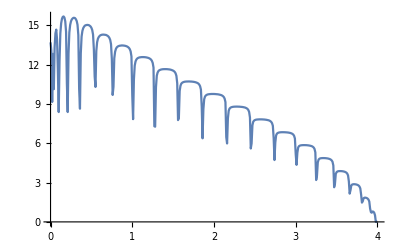

```mathematica
ListPlot[%435,Joined->True]
```

```mathematica
device7[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,10}], μ2=RandomInteger[{1,10}], μ3=RandomInteger[{11,20}], μ4=RandomInteger[{11,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4},{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp4,imp5,imp8,imp7,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[20]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[20]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[20]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
Table[{ω,Mean[Table[device7[ω,0.5,20],2000]]},{ω,Range[0,4,0.01]}]
```

$Aborted

```mathematica
testhori[ϵ1_,m_,y_,x_]:=Module[{Tin=T[1,m],T1=T[1,m](*,μ1=RandomInteger[{1,10}], μ2=RandomInteger[{1,10}], μ3=RandomInteger[{11,20}], μ4=RandomInteger[{11,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}]*),list,tra},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]];
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{15,15}}->ω+ⅈ*0.0001-ϵ1]]];
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{16,16}}->ω+ⅈ*0.0001-ϵ1]]];
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{17,17}}->ω+ⅈ*0.0001-ϵ1]]];
imp18:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{18,18}}->ω+ⅈ*0.0001-ϵ1]]];
imp19:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{19,19}}->ω+ⅈ*0.0001-ϵ1]]];
imp20:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{20,20}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
tra[start_,stop_]:=Module[{},list={{imp,imp17,imp4,imp,imp14,imp,imp10,imp,imp5,imp,imp19,imp,imp6,imp,imp8,imp,imp2,imp12,imp,imp13}};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[20]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[20]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[20]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
m1=Table[{ω,tra[1,5]},{ω,Range[0,4,0.01]}];
m2=Table[{ω,tra[6,10]},{ω,Range[0,4,0.01]}];m3=Table[{ω,tra[11,15]},{ω,Range[0,4,0.01]}];m4=Table[{ω,tra[16,20]},{ω,Range[0,4,0.01]}];
(*{m1[[1]],m2[[1]],m3[[1]],m4[[1]]}
*);
υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%429[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%430[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%431[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%432[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%433[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%435[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ2=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%429[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%430[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%431[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%432[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%433[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%435[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ3=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%429[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%430[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%431[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%432[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%433[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%435[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ4=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%429[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%430[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%431[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%432[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%433[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%435[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];{υ1,υ2,υ3,υ4}]
```

```mathematica
hori=testhori[0.5,20,0,3.5]
```

{{0.0152103,0.00922447,0.00509091,0.00412856,0.00618953,0.0114744},{0.00425335,0.00245976,0.00262664,0.00562612,0.010859,0.0176054},{0.0195364,0.0125968,0.00832377,0.00841828,0.0112797,0.0155941},{0.00815054,0.00662971,0.00625869,0.00847818,0.0132625,0.0195294}}

```mathematica
Table[Position[hori[[x]],Min[hori[[x]]]],{x,4}]
```

{{{4}},{{2}},{{3}},{{3}}}

```mathematica
testverti[ϵ1_,m_,y_,x_]:=Module[{Tin=T[1,m],T1=T[1,m](*,μ1=RandomInteger[{1,10}], μ2=RandomInteger[{1,10}], μ3=RandomInteger[{11,20}], μ4=RandomInteger[{11,20}],μ5=RandomInteger[{1,20}], μ6=RandomInteger[{1,20}], μ7=RandomInteger[{1,20}],μ8=RandomInteger[{1,20}], μ9=RandomInteger[{1,20}], μ10=RandomInteger[{1,20}], μ11=RandomInteger[{1,20}],μ12=RandomInteger[{1,20}], μ13=RandomInteger[{1,20}], μ14=RandomInteger[{1,20}]*),list,tra},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]];
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{15,15}}->ω+ⅈ*0.0001-ϵ1]]];
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{16,16}}->ω+ⅈ*0.0001-ϵ1]]];
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{17,17}}->ω+ⅈ*0.0001-ϵ1]]];
imp18:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{18,18}}->ω+ⅈ*0.0001-ϵ1]]];
imp19:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{19,19}}->ω+ⅈ*0.0001-ϵ1]]];
imp20:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{20,20}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
tra[start_,stop_]:=Module[{},list={{imp,imp17,imp,imp3,imp9,imp13,imp,imp15,imp,imp7,imp,imp18,imp20,imp5,imp,imp,imp2,imp,imp11,imp}};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[20]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[20]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[20]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
m1=Table[{ω,tra[1,5]},{ω,Range[0,4,0.01]}];
m2=Table[{ω,tra[6,10]},{ω,Range[0,4,0.01]}];
m3=Table[{ω,tra[11,15]},{ω,Range[0,4,0.01]}];
m4=Table[{ω,tra[16,20]},{ω,Range[0,4,0.01]}];
(*{m1[[1]],m2[[1]],m3[[1]],m4[[1]]}
*)υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%429[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%430[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%431[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%432[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%433[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-%435[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ2=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%429[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%430[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%431[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%432[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%433[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-%435[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ3=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%429[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%430[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%431[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%432[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%433[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-%435[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ4=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%429[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%430[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%431[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%432[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%433[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-%435[[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];{υ1,υ2,υ3,υ4}]
```

```mathematica
verti=testverti[0.5,20,0,3.8]
```

{{0.0111635,0.00685747,0.00428611,0.00488127,0.00828036,0.0137978},{0.0182341,0.0109283,0.00666103,0.0065472,0.00914695,0.0136782},{0.0085809,0.00549114,0.00648101,0.00941095,0.0127202,0.016454},{0.00606804,0.00338716,0.00408469,0.00727005,0.01179,0.0170903}}

```mathematica
Table[Position[verti[[x]],Min[verti[[x]]]],{x,4}]
```

{{{3}},{{4}},{{2}},{{2}}}

```mathematica
Dimensions[Range[0,8.5,0.01]]
```

```mathematica
{851}*5
```

```mathematica
{4255}/60
```

{851/12}

```mathematica
N[{851/12}]
```

{70.9167}